# QFT MIDTERM PROJECT

## Scalar Field Renormalization : From One Loop to the Critical Isotherm of Water

## 0. Packages and Computational Setup

$LoadAddOns={"FeynArts"};

<<FeynCalc`

FeynCalc 10.2.1 (stable version). For help, use the online documentation, visit the forum and have a look at the supplied examples. The PDF-version of the manual can be downloaded here.

If you use FeynCalc in your research, please evaluate FeynCalcHowToCite[] to learn how to cite this software.

Please keep in mind that the proper academic attribution of our work is crucial to ensure the future development of this package!

FeynArts 3.12 (27 Mar 2025) patched for use with FeynCalc, for documentation see the manual or visit www.feynarts.de.

If you use FeynArts in your research, please cite

• T. Hahn, Comput. Phys. Commun., 140, 418-431, 2001, arXiv:hep-ph/0012260

(*Model Directories*)
feynArtsDirectory="C:\Users\PC\AppData\Roaming\Wolfram\Applications\FeynCalc\FeynArts";

modelDirectory=FileNameJoin[{feynArtsDirectory,"Models"}];

phi4ExampleDirectory="C:\Users\PC\AppData\Roaming\Wolfram\Applications\FeynCalc\Examples\Models\Phi4";

(*Verifying package availability and directories*)
{MemberQ[$Packages,"FeynCalc`"],MemberQ[$Packages,"FeynArts`"],DirectoryQ[modelDirectory],DirectoryQ[phi4ExampleDirectory]}

{True,True,True,True}

## 1. FeynArts Model Setup

```mathematica
(*Copying the supplied FeynArts model files into the FeynArts Models directory so that FeynArts can locate them.*)
Scan[Function[file,CopyFile[FileNameJoin[{phi4ExampleDirectory,file}],FileNameJoin[{modelDirectory,file}],OverwriteTarget->True]],{"Phi4.mod","Phi4.gen","Phi4.pars"}];
FileNames["Phi4.*",modelDirectory]
```

{C:\Users\PC\AppData\Roaming\Wolfram\Applications\FeynCalc\FeynArts\Models\Phi4.gen,C:\Users\PC\AppData\Roaming\Wolfram\Applications\FeynCalc\FeynArts\Models\Phi4.mod,C:\Users\PC\AppData\Roaming\Wolfram\Applications\FeynCalc\FeynArts\Models\Phi4.pars}

```mathematica
(*In order to load and test the  model, we first need to patch the model files for FeynCalc*)
FAPatch[PatchModelsOnly->True];
```

Successfully patched FeynArts.

```mathematica
(*Specifying the classes model and generic model used for Feynman-diagram generation.*)
phi4ModelOptions={InsertionLevel->{Particles},Model->"Phi4",GenericModel->"Phi4"};
```

## PART 1—ONE LOOP AND TWO REGULATORS

We work in Euclidean signature with m^2 > 0 and spacetime dimension d = 4 - ϵ. The dimensionless coupling is defined as g = λ/(16 π^2) .
In dimensional regularization, we include one factor of μ^ϵ per loop . For the sharp - cutoff calculation, we work directly in four dimensions . FeynCalc uses the convention  , so the project parameter and FeynCalc parameter are related by .

### 1.1 One - Loop Diagrams

In this section, we evaluate the one-loop corrections to the two-point and four-point 1PI functions in the scalar  theory. We begin in 1.1.1 by defining the Euclidean action, establishing our mass dimensions and dimensional-regularization conventions, and listing the Feynman rules derived from the path-integral formulation. In 1.1.2, we identify the tadpole diagram, discuss its momentum-independent nature, and perform the analytical derivation of its contribution to the self-energy. We proceed in 1.1.3 to analyze the -, -, and -channels of the four-point function, defining the bubble integral  that describes the one-loop correction. In 1.1.4 we map the FeynArts topologies to the physical channels and verify the symmetry factors. In 1.1.5 we identify the FeynArts model with our conventions and fix the Wick rotation, loop measure and sign convention. In 1.1.6 we convert the amplitudes with FeynCalc and reduce them with ToPaVe. In 1.1.7 we match the resulting PaVe forms to the Euclidean one-loop contributions.

#### 1.1.1 Model and Feynman Rules

We consider a real scalar field  with quartic self-interaction in (d = 4 - ϵ) spacetime dimensions. The theory is defined by the Euclidean action 

                                                                                                                                                                       (A-01)                                                                                                                                                                  

Here,  is the dimensionless quartic coupling,  is the dimensional-regularization scale, and . The factor  is introduced so that the coupling  remains dimensionless when the spacetime dimension is analytically continued away from four dimensions.
We use the Euclidean path-integral convention:

                                                                                                                                

Consequently, the interaction contribution enters the perturbative expansion with a minus sign. This sign convention will be important when distinguishing the interaction vertex used in perturbative diagrams from the tree-level four-point 1PI vertex.

Proof: The coupling  is dimensionless, while the combination  has the required mass dimension  of the quartic coupling in  dimensions.
First, We need to determine the mass dimensions of the field and the parameters. We use natural units, in which the action is dimensionless: . Since  the Lagrangian density must have mass dimension . 
Now, Consider the kinetic term in the action. Since a spacetime derivative has  we have:

                                                                                                                               (A-02)
                                           
Now, let’s focus on the interaction term and use the relation we found for mass dimension of the scalar field. Note that  is a mass scale. Keeping this in mind, we have:

                                                                

But we have: . Therefore, we conclude  and the coupling is dimensionless, while the combination  has the required mass dimension  of the quartic coupling in  dimensions.

Free theory and the propagator:
We first separate the action into its quadratic and interaction parts:  where:

                                                                                           and           

To identify the free propagator, we rewrite the quadratic action in operator form. Assuming that boundary terms vanish, integration by parts gives:

                                                                                                                 

where   is the Euclidean Laplacian. Therefore,

                                                                                                                          

The differential operator appearing in this expression is the inverse free propagator in position space. To obtain its momentum-space form, we use the Fourier convention:

                                                                                                                              

Under this transformation, derivatives act as  and hence  The quadratic action consequently becomes:

                                                                                                                     

The free propagator is the inverse of the quadratic momentum-space operator. Thus, the Euclidean scalar propagator is:

                                                                                                                                                                                                                                    (A-03)

Quartic interaction vertex:
Consider the quartic interaction term in the Euclidean action. To obtain the interaction vertex, we expand the Euclidean path-integral weight: 
Therefore, the first-order interaction contribution carries a minus sign. The factor 1/4! in the action cancels the 4! possible contractions of the four identical scalar fields with the external lines. Consequently, the quartic interaction vertex in the Euclidean perturbative Feynman rules is:

                                                                                                                                                                                                                                                         (A-04)

Note that the negative sign comes from expanding , and therefore belongs to the perturbative Feynman-rule vertex. It should not be confused with the tree-level four-point 1PI vertex, which is obtained by differentiating the classical Euclidean action four times with respect to the field. At tree level, this gives  
Thus, the perturbative interaction vertex is negative, whereas the tree-level four-point 1PI vertex is positive. According to the convention adopted in this project, we strip the overall factor  from the tree-level 1PI vertex and write  (A-05)

Dimensional-regularization loop measure:
In dimensional regularization, loop momenta are integrated over  dimensions. Each independent loop integration is accompanied by one factor of . Thus, for a diagram with L independent loops, the dimensional-regularization scale contributes an overall factor .
For a single loop, the integration measure is therefore written as: 

                                                                                                                                                                                                                                              (A-06)

Again note that: In this project, the overall tree-level factor  is stripped from the four-point 1PI vertex, while the factor  associated with each loop integration is retained. This convention must be applied consistently when evaluating loop diagrams and comparing the results obtained using different regularization schemes.

```mathematica
(*---Parameters and Conventions---*)
ClearAll[d,e,muR,lam,m2,iProp,Prop,v4,v4tree,dloop];

(*d:dimension, e:epsilon*)
d=4-e;

(*muR:Renormalization scale,lam:Coupling,m2:Mass squared*)
assumptions={e,muR,lam,m2}∈Reals&&m2>0&&muR>0;

(*---Propagators---*)

(*Inverse propagator:D^-1=k^2+m^2*)
iProp[k_]:=k^2+m2;

(*Scalar propagator:D=1/(k^2+m^2)*)
Prop[k_]:=1/iProp[k];

(*---Vertices---*)

(*Tree-level four-point vertex:overall muR^e stripped*)
v4tree=lam;
(*Interaction vertex used in the Euclidean diagrams*)
v4=-lam;

(*---Dimensional-Regularization Loop Measure---*)
(*One muR^e factor per independent loop*)
dloop[k_]:=muR^e/(2 Pi)^d;
```

--------------------------------------------------------------------------------------------------------------------------------------------------------------------------------

#### 1.1.2 Two-Point Function

At one loop, the two - point function receives a contribution from the tadpole diagram . The diagram contains one quartic interaction vertex . Two of its four legs are attached to the external lines, while the remaining two legs are contracted with each other to form an internal propagator loop . There are no other one-loop 1PI topologies for the two - point function in a theory with only a quartic interaction vertex . Diagrams that can be separated into disconnected pieces by cutting one internal line are one - particle reducible and are therefore not included in the 1PI two-point function.

Momentum assignment:
We assign incoming momentum  to the left external leg and outgoing momentum  to the right external leg. Let  denote the loop momentum circulating in the internal propagator. Momentum conservation at the quartic vertex is then satisfied: 
The internal propagator carries momentum , and its Euclidean expression is  Since the two external momenta enter and leave the same vertex, the loop propagator does not depend on . This already indicates that the one-loop tadpole correction is momentum independent.

Symmetry factor:
We can obtain this factor directly from the interaction term. At first order in the coupling, the Euclidean path integral contains  To construct the two-point contribution, we differentiate twice with respect to the external fields. The four identical fields at the vertex can be differentiated in  ways. Thus, the combinatorial coefficient is  
Therefore, the tadpole diagram carries a symmetry factor of . (A-07)

Euclidean Loop Integral:
Incorporating the vertex factor  and the symmetry factor, the one-loop self-energy is: (See Fields Notes §12.)

                                                                                                                                                                                                        (A-08)

Note: The sign above reflects the Euclidean convention   with the vertex factor .

The full two-point 1PI function is: (See Fields Notes §12.)

                                                                                                                                                                                                                (A-09)

The tadpole integral, defined as:  will be evaluated in subsection 1.2. (A-10)

Important computational note: FeynArts generates amplitudes using its own conventions. The conversion to FeynCalc does not, by itself, establish the Euclidean expression. Therefore, we must state the Wick rotation and use the Euclidean propagator and loop measure consistently when comparing the converted result with the above equations.

loading generic model file C:\Users\PC\AppData\Roaming\Wolfram\Applications\FeynCalc\FeynArts\Models\Phi4.gen

> $GenericMixing is OFF

generic model {Phi4} initialized

loading classes model file C:\Users\PC\AppData\Roaming\Wolfram\Applications\FeynCalc\FeynArts\Models\Phi4.mod

> 1 particles (incl. antiparticles) in 1 classes

> $CounterTerms are ON

> 1 vertices

> 2 counterterms of order 1

classes model {Phi4} initialized

inserting at level(s) {Particles}

> Top. 1: 1 Particles insertion

in total: 1 Particles insertion

> Top. 1 ac\bc\cc.m, 0 diagrams

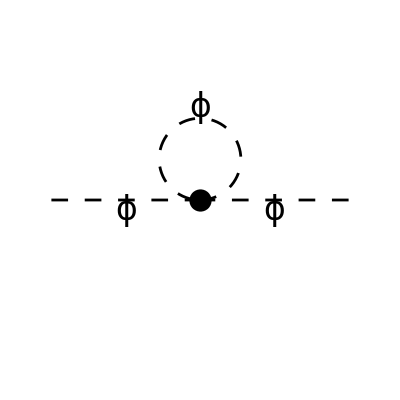

FeynArtsGraphics()(([]))

```mathematica
(*---1. Generate the one-loop two-point topology---*)twoPointTopologies=CreateTopologies[1,1->1,Adjacencies->{4}];

(*---2. Insert the scalar fields---*)

twoPointInsertions=InsertFields[twoPointTopologies,{S[1]}->{S[1]},Sequence@@phi4ModelOptions];

(*---3. Display the generated Feynman diagrams---*)

Paint[twoPointInsertions,ColumnsXRows->{1,1},Numbering->None,SheetHeader->None]
```

```mathematica
(*---4. Construct the FeynArts amplitude---*)

twoPointFeynArtsAmplitude=CreateFeynAmp[twoPointInsertions,Truncated->True];

(*---5. Convert the amplitude to FeynCalc notation---*)

twoPointFeynCalcAmplitude=FCFAConvert[twoPointFeynArtsAmplitude,IncomingMomenta->{p},OutgoingMomenta->{p},LoopMomenta->{k},ChangeDimension->D];

(*---6. Display the converted amplitude---*)

twoPointFeynCalcAmplitude
```

creating amplitudes at level(s) {Particles}

> Top. 1: 1 Particles amplitude

in total: 1 Particles amplitude

{-(ⅈ g)/(32 π^4 (k^2-mphi^2))}

Note on the coupling and conventions : 
The coupling  appearing in the converted amplitude is the quartic coupling parameter defined in the FeynArts model “Phi4 . mod”. It has not yet been identified with the dimensionless coupling  introduced in the project . The correspondence between the FeynArts coupling and the analytical coupling , including the normalization, will be established when matching the FeynArts amplitudes to the conventions of the analytical calculation . Furthermore, the converted expression is still in Minkowski - space form . The Wick rotation and the corresponding loop - measure conventions will be discussed separately in subsection 1.1.5 .
------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------

#### 1.1.3 Four-Point Function

At one loop, the four-point 1PI function receives contributions from three distinct channels: the  and  channels. Each contribution is represented by a bubble diagram consisting of two quartic interaction vertices connected by two internal propagators. These diagrams provide the  correction to the four-point 1PI function.

Momentum assignment: 
Let the four external momenta be , all taken to be incoming, so that momentum conservation requires  The three channels correspond to the following pairings of external legs:

                                (A-11)

In each channel, the two internal propagators carry momenta k and k+P, where P denotes the total external momentum entering one of the two vertices. By momentum conservation, the total momentum entering the other vertex is -P. The three diagrams share the same topological structure, differing only in the external momentum flowing through the loop.

Symmetry factor and interaction vertices: 
Each bubble diagram has a symmetry factor of , arising from the interchange symmetry of the two internal propagators.  The two quartic interaction vertices give a contribution proportional to . Thus, the overall coefficient of each one-loop bubble contribution is  .  (A-12)
With the Euclidean perturbative interaction vertex  established in Section 1.1.1, the resulting one-loop correction to the four-point 1PI function carries a negative sign, consistent with the Euclidean conventions used in Zamolodchikov, Section 12.

Euclidean loop integral: 
Following the conventions of Fields Notes, Section 12, we define the standard massive bubble integral as:

                                                                                                                                                                     (A-13)

The function  represents the one-loop bubble integral arising from the four-point 1PI diagrams. It depends on the total external momentum flowing through the loop and the scalar mass. Its evaluation will be used to determine the one-loop correction to the four-point function and its ultraviolet divergences.
The -channel contribution to the four-point 1PI function is consequently: 

                                                                                                                                                                                                                                    (A-14)
                                                                                                                                     
The  and  channel contributions follow by replacing  with  and , respectively. Including the tree-level contribution, the complete four-point 1PI function at this order is:

                                                                                                                                                                                            (A-15)

Here, the overall  factor is included in the definition of each bubble integral, as required by dimensional regularization.
Reference: The definition of  and its role in the 1PI function are derived in Zamolodchikov §12.

Computational note: 
FeynArts will generate the one-loop four-point diagrams and their external-momentum assignments. We will subsequently examine their amplitudes and symmetry factors, convert them into FeynCalc expressions, and use ToPaVe to reduce the resulting loop integrals. The correspondence between the converted integrals and the bubble function  will be checked for each of the three channels.

inserting at level(s) {Particles}

> Top. 1: 1 Particles insertion

> Top. 2: 1 Particles insertion

> Top. 3: 1 Particles insertion

in total: 3 Particles insertions

> Top. 1 aebe\cfdf\efef.m, 0 diagrams

> Top. 2 aebf\cedf\efef.m, 0 diagrams

> Top. 3 aebf\cfde\efef.m, 0 diagrams

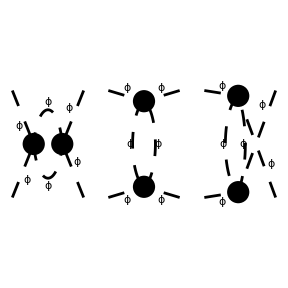

FeynArtsGraphics()(([] | [] | []))

```mathematica
ClearAll[bubbleTopologies,bubbleInsertions];
(*---1. Generate one-loop 1PI 4-point topologies---*)bubbleTopologies=CreateTopologies[1,2->2,Adjacencies->{4},ExcludeTopologies->{Reducible}];

(*---2. Insert the scalar fields---*)

bubbleInsertions=InsertFields[bubbleTopologies,{S[1],S[1]}->{S[1],S[1]},Sequence@@phi4ModelOptions];

(*---3. Display the generated diagrams---*)

Paint[bubbleInsertions,ColumnsXRows->{3,1},Numbering->None,SheetHeader->None]
```

```mathematica
(*---4. Generate FeynArts amplitudes---*)bubbleFeynArtsAmplitude=CreateFeynAmp[bubbleInsertions,Truncated->True];

(*---5. Convert to FeynCalc expressions---*)

bubbleFeynCalcAmplitude=FCFAConvert[bubbleFeynArtsAmplitude,IncomingMomenta->{p1,p2},OutgoingMomenta->{p3,p4},LoopMomenta->{k},ChangeDimension->D];

(*---6. Display the results---*)

bubbleFeynArtsAmplitude

bubbleFeynCalcAmplitude
```

creating amplitudes at level(s) {Particles}

> Top. 1: 1 Particles amplitude

> Top. 2: 1 Particles amplitude

> Top. 3: 1 Particles amplitude

in total: 3 Particles amplitudes

FAFeynAmpList(Process→(S(1) | p1 | mphi | {}
S(1) | p2 | mphi | {})→(S(1) | k1 | mphi | {}
S(1) | k2 | mphi | {}),Model→{Phi4},GenericModel→{Phi4},AmplitudeLevel→{Particles},ExcludeParticles→{},ExcludeFieldPoints→{},LastSelections→{})(FAFeynAmp(GraphID(Topology==1,Generic==1,Particles==1,Number==1),Integral[q1],-(ⅈ g^2 FAFeynAmpDenominator(1/((q1)^2-mphi^2),1/((-k1-k2+q1)^2-mphi^2)))/(32 π^4)),FAFeynAmp(GraphID(Topology==2,Generic==1,Particles==1,Number==2),Integral[q1],-(ⅈ g^2 FAFeynAmpDenominator(1/((q1)^2-mphi^2),1/((-k2+p2+q1)^2-mphi^2)))/(32 π^4)),FAFeynAmp(GraphID(Topology==3,Generic==1,Particles==1,Number==3),Integral[q1],-(ⅈ g^2 FAFeynAmpDenominator(1/((q1)^2-mphi^2),1/((-k1+p2+q1)^2-mphi^2)))/(32 π^4)))

{-(ⅈ g^2)/(32 π^4 (k^2-mphi^2).((k-p3-p4)^2-mphi^2)),-(ⅈ g^2)/(32 π^4 (k^2-mphi^2).((k+p2-p4)^2-mphi^2)),-(ⅈ g^2)/(32 π^4 (k^2-mphi^2).((k+p2-p3)^2-mphi^2))}

Note on the coupling and conventions :
The coupling  appearing in the converted amplitude is the quartic coupling parameter defined in the FeynArts model “Phi4 . mod”. It has not yet been identified with the dimensionless coupling  introduced in the project . The correspondence between the FeynArts coupling and the analytical coupling , including the normalization, will be established when matching the FeynArts amplitudes to the conventions of the analytical calculation . Furthermore, the converted expression is still in Minkowski - space form . The Wick rotation and the corresponding loop - measure conventions will be discussed separately in subsection 1.1.5 .
--------------------------------------------------------------------------------------------------------------------------------------------------------------------------------

#### 1.1.4 Mapping and Symmetry Verification

In this subsection, we map the topologies generated by FeynArts to the physical channels defined in our analytical framework and verify their corresponding symmetry factors . This provides a consistency check between the automatically generated diagrams and the analytical Feynman - diagram expansion . 

Channel Mapping:
The three one - loop 1 PI topologies generated by FeynArts correspond to the and  channel contributions to the four-point function . Each generated diagram is identified by its GraphID. By examining the external momentum routing and the pairing of external legs at the two interaction vertices, we associate each diagram with its corresponding channel :   where all external momenta are taken to be incoming and satisfy  (A-16)
FeynArts, however, uses two incoming momenta  and two outgoing momenta . With this convention, the momentum transfers appearing in the generated amplitudes are , , and , corresponding to the , and -channels, respectively. These transfers differ by an overall minus sign from the corresponding analytical definitions in the - and -channels. This does not affect the bubble integrals because they are invariant under .

Symmetry Factors:
The analytical symmetry factors are obtained from the functional-derivative expansion of the interaction term, as established in Fields Notes, §12. Both the one-loop tadpole diagram contributing to the two-point function and each one-loop bubble diagram contributing to the four-point function have a symmetry factor of 1/2. (A-17)
We examine the consistency of these factors with the amplitudes generated by FeynArts. In the displayed four-dimensional normalization, the numerical prefactor of each generated amplitude contains  which is consistent with a symmetry factor of 1/2 multiplying the conventional loop measure.
The generated amplitudes are proportional to  for the tadpole and  for each bubble diagram, where  denotes the coupling parameter of the FeynArts model. The identification of this parameter with the analytical coupling , together with the complete normalization and sign conventions, will be established when matching the FeynArts amplitudes to the analytical expressions in subsection 1.1.5 to 1.1.7.

```mathematica
(*Extract GraphIDs from the two-point amplitude*)twoPointGraphIDs=Cases[twoPointFeynArtsAmplitude,graphID_GraphID:>graphID,Infinity];

(*Extract GraphIDs from the four-point amplitudes*)
bubbleGraphIDs=Cases[bubbleFeynArtsAmplitude,graphID_GraphID:>graphID,Infinity];

(*Display the GraphID information*)
Print["Two-point GraphIDs: ",twoPointGraphIDs];

Print["Four-point GraphIDs: ",bubbleGraphIDs];

(*Map four-point diagrams to physical channels*)
(*The mapping follows from inspecting the external momentum routing in the generated FeynArts amplitudes.*)

bubbleChannelMapping={{bubbleGraphIDs[[1]],"s-channel","p1 + p2"},{bubbleGraphIDs[[2]],"t-channel","p2 - k2"},{bubbleGraphIDs[[3]],"u-channel","p2 - k1"}};

Grid[Prepend[bubbleChannelMapping,{"GraphID","Channel","External Momentum Transfer"}],Frame->All,Alignment->Center];

(*Display the amplitudes for symmetry-factor verification*)

Print["Two-point FeynArts amplitude:"];

twoPointFeynArtsAmplitude

Print["Four-point FeynArts amplitudes:"];

bubbleFeynArtsAmplitude
```

Two-point GraphIDs: {GraphID(Topology==1,Generic==1,Particles==1,Number==1)}

Four-point GraphIDs: {GraphID(Topology==1,Generic==1,Particles==1,Number==1),GraphID(Topology==2,Generic==1,Particles==1,Number==2),GraphID(Topology==3,Generic==1,Particles==1,Number==3)}

Two-point FeynArts amplitude:

FAFeynAmpList(Process→(S(1) | p1 | mphi | {})→(S(1) | k1 | mphi | {}),Model→{Phi4},GenericModel→{Phi4},AmplitudeLevel→{Particles},ExcludeParticles→{},ExcludeFieldPoints→{},LastSelections→{})(FAFeynAmp(GraphID(Topology==1,Generic==1,Particles==1,Number==1),Integral[q1],-(ⅈ g FAFeynAmpDenominator(1/((q1)^2-mphi^2)))/(32 π^4)))

Four-point FeynArts amplitudes:

FAFeynAmpList(Process→(S(1) | p1 | mphi | {}
S(1) | p2 | mphi | {})→(S(1) | k1 | mphi | {}
S(1) | k2 | mphi | {}),Model→{Phi4},GenericModel→{Phi4},AmplitudeLevel→{Particles},ExcludeParticles→{},ExcludeFieldPoints→{},LastSelections→{})(FAFeynAmp(GraphID(Topology==1,Generic==1,Particles==1,Number==1),Integral[q1],-(ⅈ g^2 FAFeynAmpDenominator(1/((q1)^2-mphi^2),1/((-k1-k2+q1)^2-mphi^2)))/(32 π^4)),FAFeynAmp(GraphID(Topology==2,Generic==1,Particles==1,Number==2),Integral[q1],-(ⅈ g^2 FAFeynAmpDenominator(1/((q1)^2-mphi^2),1/((-k2+p2+q1)^2-mphi^2)))/(32 π^4)),FAFeynAmp(GraphID(Topology==3,Generic==1,Particles==1,Number==3),Integral[q1],-(ⅈ g^2 FAFeynAmpDenominator(1/((q1)^2-mphi^2),1/((-k1+p2+q1)^2-mphi^2)))/(32 π^4)))

```mathematica
(*Check the numerical symmetry-factor prefactor*)
(*In four dimensions,the conventional loop measure contributes 1/(2 Pi)^4.*)

feynArtsLoopMeasure4D=1/(2 Pi)^4;

feynArtsNumericalPrefactor=1/(32 Pi^4);

feynArtsSymmetryFactor=FullSimplify[feynArtsNumericalPrefactor/feynArtsLoopMeasure4D];

Print["Numerical symmetry-factor prefactor: ",feynArtsSymmetryFactor];
(*Each term is understood to be multiplied by the loop integration measure:∫d^d k.The displayed expression shows only the common prefactor.*)
```

Numerical symmetry-factor prefactor: 1/2

--------------------------------------------------------------------------------------------------------------------------------------------------------------------------------

#### 1.1.5 Model identification

FeynArts and FeynCalc work in Minkowski signature with their own factors of , while this project is Euclidean. Before reading any generated amplitude we fix the dictionary between the two. Sections 1.1.6 and 1.1.7 then only apply it.

Model identification:
The model is defined by Phi4.mod, Phi4.gen and Phi4.pars. They give the propagator and vertex

                                                                                                                                                                                                    (A-18)

Phi4.pars sets the wave-function, mass and coupling renormalization factors to 1, so no counterterm diagrams appear at this stage. The parameters are identified as   Here  is the unrescaled quartic coupling. It is not the rescaled coupling  used for the RG in 1.4. (A-19)

Wick rotation:
Set  and . Then

                                                                           

After the rotation the denominator is positive definite, so the  is no longer needed. The vertex  does not change. A Minkowski invariant maps to its Euclidean counterpart as . In particular  and   in terms of the Euclidean invariants. (A-20)

Loop measure:
Each loop carries one factor of , with : . FeynCalc uses , so  throughout.                        (A-21)

Sign convention:
The Euclidean vertex from  is , which is different from the tree-level  (see 1.1.1). The 1PI functions are

                                                               

At one loop, with symmetry factor 1/2 for each diagram,

                                                                                                              ,                                                           (A-22)

Expected dictionary to PaVe functions:
Applying weak rotation and loop measure to  gives . The PaVe normalization gives . 
Doing the same for the bubble gives:

                                                                                                                                                                                  (A-23)

Combined with the sign convention, the converted FeynCalc results of 1.1.6 should satisfy:

                                                                                                                                                                                                      (A-24)

This is a prediction. It is tested explicitly in 1.1.7, and the normalization of  and  must be confirmed against the actual output.

```mathematica
faToProject={g->lam,mphi->Sqrt[m2]};

(*Step 2:perturbative Euclidean vertex from exp(-S_int) (A-03,A-15).v4 and v4tree were already defined in 1.1.1;repeated here so that this cell can be evaluated on its own.*)
v4=-lam;
v4tree=lam;

(*Step 3:epsilon convention (A-14).d=4-e was set in 1.1.1;FeynCalc uses D=4-2 epsFC,hence e=2 epsFC.*)
eRule=e->2 epsFC;

(*Step 4:channel momenta,all incoming (A-07).Ps2,Pt2,Pu2 are plain symbols for the Euclidean invariants Ps.Ps,Pt.Pt,Pu.Pu;they are not expanded in p1,...,p4.*)
Ps=p1+p2;
Pt=p1+p3;
Pu=p1+p4;

(*Step 5:Wick dictionary for invariants (A-13):Mandelstam=-Euclidean invariant*)
mandelstamToEuclidean={s->-Ps2,t->-Pt2,u->-Pu2};

(*Step 6:expected PaVe<->Euclidean-integral dictionary (A-16).It is tested explicitly in 1.1.7.*)
euclideanToPaVe={TDR[x_]:>-A0[x]/(16 Pi^2),BDR[P2_,x_]:>B0[-P2,x,x]/(16 Pi^2)};

(*Step 7:display the dictionary*)
Print["FeynArts -> project parameter map:"];
faToProject
Print["Epsilon convention (FeynCalc D = 4 - 2 epsFC):"];
eRule
Print["Euclidean vertex and tree vertex:"];
{v4,v4tree}
Print["Wick dictionary for the channel invariants:"];
mandelstamToEuclidean
Print["Expected PaVe dictionary:"];
euclideanToPaVe
```

FeynArts -> project parameter map:

{g→lam,mphi→√m2}

Epsilon convention (FeynCalc D = 4 - 2 epsFC):

e→2 epsFC

Euclidean vertex and tree vertex:

{-lam,lam}

Wick dictionary for the channel invariants:

{s→-Ps2,t→-Pt2,u→-Pu2}

Expected PaVe dictionary:

{TDR(x_):>-(A_0(x))/(16 π^2),BDR(P2_,x_):>(B_0(-P2,x,x))/(16 π^2)}

#### 1.1.6 FeynCalc Conversion and PaVe Reduction

The FeynArts amplitudes are converted with FCFAConvert. The external momenta and the loop momentum are given explicitly so that the routing is unambiguous. The converted amplitudes are then reduced with TID[..., ToPaVe -> True]. The  convention of 1.1.5 applies throughout.

The reduced amplitudes are:

                                                                                                                                                (A-25)

Each prefactor is the symmetry factor , times the vertex factors, times the  of the PaVe normalization.
SetMandelstam is used here only to label the three channels in FeynCalc’s output. It declares on-shell external legs, which is not assumed in Part 1, where  is generic. In the FeynArts convention (two incoming, two outgoing) the momentum transfers in the  and  channels may carry the opposite orientation from the all-incoming  and  of 1.1.5. The bubble is even in , so this does not matter.
The PaVe functions stay symbolic here. Their comparison with the Euclidean integrals is made in 1.1.7, and their evaluation is in 1.2.

```mathematica
(*Step 1:tensor reduction to PaVe functions*)twoPointPaVe=TID[#,k,ToPaVe->True]&/@twoPointFeynCalcAmplitude;
bubblePaVe=TID[#,k,ToPaVe->True]&/@bubbleFeynCalcAmplitude;

(*Step 2:simplify;expand scalar products in the four-point result*)
twoPointPaVeSimplified=Simplify/@twoPointPaVe;
bubblePaVeExpanded=ExpandScalarProduct/@(Simplify/@bubblePaVe);

(*Step 3:Mandelstam variables,labelling only (external legs on shell)*)
FCClearScalarProducts[];
SetMandelstam[s,t,u,p1,p2,-p3,-p4,mphi,mphi,mphi,mphi];

(*Step 4:external notation and Mandelstam relations*)
twoPointPaVeReadable=FCE[twoPointPaVeSimplified];
bubblePaVeMandelstam=Simplify[FCE[bubblePaVeExpanded]];

(*Step 5:display*)
Print["Two-point amplitude in PaVe representation:"];
twoPointPaVeReadable//StandardForm

Print["Four-point amplitudes in PaVe representation:"];
bubblePaVeMandelstam//StandardForm
```

Two-point amplitude in PaVe representation:

{(g A0[mphi^2])/(32 π^2)}

Four-point amplitudes in PaVe representation:

{(g^2 B0[s,mphi^2,mphi^2])/(32 π^2),(g^2 B0[t,mphi^2,mphi^2])/(32 π^2),(g^2 B0[u,mphi^2,mphi^2])/(32 π^2)}

#### 1.1.7 Euclidean Matching of the One-Loop Contributions

With the dictionary of 1.1.5, the Euclidean building blocks are the integrands   and the integrals  and  defined in 1.2. The three four-point channels use  with ,  and .
With  and the symmetry factors of 1.1.2 to 1.1.4, the one-loop contributions to the 1PI functions are:

                                                                                                          

Consistency check against 1.1.6:
 After the identification , the PaVe results of 1.1.6 must equal minus these contributions under the dictionary (A-24). The cells below test this. If a check fails, inspect the sign or factor of  in 1.1.5 instead of adjusting the result to force a zero. (A-26)
The explicit evaluation of  and  is done in 1.2.

```mathematica
(*Step 0:FeynArts prints its quartic coupling as g (not gFA) and the mass as mphi.Identification (A-12):g_FA=lam,mphi^2=m2.TDR and BDR must stay inert here;they are defined in 1.2.3.*)
faToProject={g->lam,mphi->Sqrt[m2]};
ClearAll[TDR,BDR];

(*Step 1:Euclidean integrands,including the DR measure (inert symbols)*)
euclideanTadpoleIntegrand[k_]:=dloop[k] Prop[k];
euclideanBubbleIntegrand[k_,P_]:=dloop[k] Prop[k] Prop[k+P];

(*Step 2:scalar integrals,evaluated in 1.2*)
tadpoleDRIntegral=TDR[m2];
bubbleDRIntegral[P2_]:=BDR[P2,m2];

(*Step 3:one-loop contributions to the 1PI functions (A-15)*)
tadpoleEuclideanContribution=-(v4/2) tadpoleDRIntegral;
bubbleEuclideanContribution[P2_]:=-(v4^2/2) bubbleDRIntegral[P2];

bubbleSChannel=bubbleEuclideanContribution[Ps2];
bubbleTChannel=bubbleEuclideanContribution[Pt2];
bubbleUChannel=bubbleEuclideanContribution[Pu2];

twoPointOneLoopCorrection=tadpoleEuclideanContribution;
fourPointOneLoopCorrection=bubbleSChannel+bubbleTChannel+bubbleUChannel;

(*Step 4:explicit-measure form of the four-point sum*)
euclideanBubbleKernel=Prop[k] Prop[k+Ps]+Prop[k] Prop[k+Pt]+Prop[k] Prop[k+Pu];
euclideanBubbleTotalFactored=-(lam^2/2) dloop[k] euclideanBubbleKernel;
(*dloop[k] stands for muR^e/(2 Pi)^d d^d k with d=4-e*)

(*Step 5:checks against the FeynCalc amplitudes (expected:0).Under the dictionary of 1.1.5(e):FeynCalc amplitude=-(Euclidean Gamma contribution).*)
tadpoleCheck=Simplify[(Total[PaVeToABCD/@Flatten[{twoPointPaVeReadable}]]/. faToProject)-((-twoPointOneLoopCorrection)/. euclideanToPaVe)];

bubbleCheck=Simplify[((Total[PaVeToABCD/@Flatten[{bubblePaVeMandelstam}]]/. faToProject)/.
mandelstamToEuclidean)-((-fourPointOneLoopCorrection)/. euclideanToPaVe)];

(*Step 6:display*)
Print["Euclidean tadpole integrand:"];
euclideanTadpoleIntegrand[k]//TraditionalForm

Print["Euclidean bubble integrand:"];
euclideanBubbleIntegrand[k,P]//TraditionalForm

Print["Tadpole contribution to Gamma2:"];
tadpoleEuclideanContribution//TraditionalForm

Print["s-, t-, u-channel bubble contributions:"];
{bubbleSChannel,bubbleTChannel,bubbleUChannel}//TraditionalForm

Print["Total one-loop Gamma4 correction:"];
fourPointOneLoopCorrection//TraditionalForm

Print["Factored four-point form:"];
euclideanBubbleTotalFactored//TraditionalForm

Print["Tadpole matching check (expected: 0):"];
tadpoleCheck

Print["Bubble matching check (expected: 0):"];
bubbleCheck
```

Euclidean tadpole integrand:

((2 π)^(e-4) muR^e)/(k^2+m2)

Euclidean bubble integrand:

((2 π)^(e-4) muR^e)/((k^2+m2) ((k+P)^2+m2))

Tadpole contribution to Gamma2:

1/2 lam TDR(m2)

s-, t-, u-channel bubble contributions:

{-1/2 lam^2 BDR(Ps2,m2),-1/2 lam^2 BDR(Pt2,m2),-1/2 lam^2 BDR(Pu2,m2)}

Total one-loop Gamma4 correction:

-1/2 lam^2 BDR(Ps2,m2)-1/2 lam^2 BDR(Pt2,m2)-1/2 lam^2 BDR(Pu2,m2)

Factored four-point form:

-2^(e-5) π^(e-4) lam^2 muR^e (1/((k^2+m2) ((k+p1+p2)^2+m2))+1/((k^2+m2) ((k+p1+p3)^2+m2))+1/((k^2+m2) ((k+p1+p4)^2+m2)))

Tadpole matching check (expected: 0):

0

Bubble matching check (expected: 0):

0

--------------------------------------------------------------------------------------------------------------------------------------------------------------------------------

#### Section 1.1—Verification Summary

Question:
What do the one-loop Feynman diagrams give, and how do their contributions map onto the Euclidean two-point and  four-point 
1PI functions,   and ?        
-----------------------------------------------------------------------------------------------------------------------------------------------------------------------------                                           
Derivation: 
Sections 1.1.1–1.1.7, with the Euclidean matching carried out in Section 1.1.5. 
-----------------------------------------------------------------------------------------------------------------------------------------------------------------------------
Check: 
Out[108] and Out[110] both evaluate to zero, confirming the corresponding consistency checks. 
-----------------------------------------------------------------------------------------------------------------------------------------------------------------------------
Anchor IDs: 
A-01 to A-26. 
-----------------------------------------------------------------------------------------------------------------------------------------------------------------------------
Status: 
Checked!

### 1.2 Cutoff and Dimensional Regularization

In this section, we evaluate the loop integrals defined in Section 1.1 using two distinct regularization schemes : the sharp momentum cutoff and dimensional regularization (DR) . We begin in 1.2.1 by formally defining the massive tadpole and bubble integrals that form the basis of our one-loop calculations . In 1.2.2, we evaluate these expressions using a sharp momentum cutoff , focusing on the identification of power-law and logarithmic divergences . We then perform the parallel evaluation in 1.2.3 using dimensional regularization, which preserves the translational symmetry of the theory . In 1.2.4, we derive the Laurent expansions of these integrals in the vicinity of , identifying the physical ultraviolet poles and their relation to the theory's renormalization. Finally, in 1.2.5, we demonstrate the validity of the derivative identity  in both schemes, confirming the regulator independence of the underlying physics as the regulators are removed.

#### 1.2.1 Definition of the Tadpole and Bubble Integrals

We begin by defining the primary loop integrals that determine the one-loop corrections to the two-point and four-point functions. In Euclidean momentum space, the massive tadpole integral is:

                                                                                                                   

This integral characterizes the momentum-independent self-energy correction. The corresponding massive bubble integral is:

                                                                                                       

where  is the total external Euclidean momentum flowing through the loop. (A-27)
Throughout our evaluation, we employ dimensional regularization with , where the renormalization scale  is associated with each loop to maintain dimensional consistency. We also consider the zero-momentum limit of the bubble integral:

                                                                                                                             

This specific integral facilitates the verification of the derivative identity:

                                                                                                                                                                                                                                                (A-28)

This identity, which follows directly from differentiating the tadpole integrand with respect to the mass squared, serves as a check for the consistency of our regularization schemes. We will formally verify this relation in subsection 1.2.5.

```mathematica
(*---1. Define Integrands using established Prop[k]---*)
tadpoleIntegrand[k_]:=Prop[k];

bubbleIntegrand[k_,P_]:=Prop[k] Prop[k+P];

zeroMomentumBubbleIntegrand[k_]:=Prop[k]^2;


(*---2. Display Formal Integral Definitions---*)
Print["Massive tadpole integral:"];

TraditionalForm[HoldForm[T[m2]==Inactive[Integrate][tadpoleIntegrand[k],{k,ℝ^d}]]]


Print["Massive bubble integral:"];

TraditionalForm[HoldForm[B[P^2]==Inactive[Integrate][bubbleIntegrand[k,P],{k,ℝ^d}]]]


Print["Zero-momentum bubble integral:"];

TraditionalForm[HoldForm[B[0]==Inactive[Integrate][zeroMomentumBubbleIntegrand[k],{k,ℝ^d}]]]
```

Massive tadpole integral:

T(m2)==Integrate[tadpoleIntegrand(k),{k,ℝ^d}]

Massive bubble integral:

B(P^2)==Integrate[bubbleIntegrand(k,P),{k,ℝ^d}]

Zero-momentum bubble integral:

B(0)==Integrate[zeroMomentumBubbleIntegrand(k),{k,ℝ^d}]

Note: The integrals above are formal definitions and are kept unevaluated using Inactive[Integrate]. The loop-measure factor   is introduced explicitly during the regularization calculations. Actual loop integrations will be performed using the appropriate methods for each regularization scheme.
------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------

#### 1.2.2 Sharp Momentum Cutoff Evaluation

We evaluate the tadpole and bubble integrals using a sharp momentum cutoff,  . In this scheme, the spacetime dimension is fixed to , and we perform the angular integration before the radial integration. This approach avoids shifting the loop momentum, thereby preserving the integration boundary and avoiding potential issues with non-invariant regularization.
The rotational symmetry of the integrands allows us to use the four-dimensional volume element , where . The tadpole integral takes the form:

                                                                                                                                                                      (A-29)

The bubble integral is similarly reduced by performing the angular integration over the three-sphere, resulting in a radial expression that depends on the external momentum :

                                                                                                                                                                                     (A-30)

In this formulation, the angular dependence of the bubble integrand is handled analytically before the radial integration. Evaluating these integrals allows us to identify the ultraviolet power-law and logarithmic divergences associated with the cutoff scale .
These cutoff-dependent results provide a clear hierarchy of UV divergences, specifically the quadratic divergence of the tadpole integral and the logarithmic divergence of the bubble integral. These results will serve as a benchmark for comparison with the dimensionally regularized results obtained in the next subsection.

```mathematica
(*---1. Define the sharp momentum cutoff---*)cutoff=Λ;

cutoffAssumptions={cutoff>0,m2>0,P2>=0};


(*---2. Evaluate the massive tadpole integral---(A-31)*)

tadpoleCutoff=FullSimplify[1/(8 Pi^2)*Integrate[k^3/(k^2+m2),{k,0,cutoff},Assumptions->cutoffAssumptions]];


(*---3. Expand the tadpole for large cutoff---(A-32)*)

tadpoleExpansion=FullSimplify[Normal[Series[tadpoleCutoff,{cutoff,Infinity,2}]]];


(*---4. Perform the angular integration for the bubble---*)

(*In four-dimensional Euclidean momentum space:d^4 k=k^3 dk dOmega_3,dOmega_3=4 Pi Sin[theta]^2 dtheta.The angular integration gives:4 Pi^2/(A+Sqrt[A^2-4 k^2 P2]),where A=k^2+m2+P2.*)

bubbleAngularIntegral[k_,P2_]:=4 Pi^2/(k^2+m2+P2+Sqrt[(k^2+m2+P2)^2-4 k^2 P2]);


(*---5. Define the radial bubble integrand---*)

(*The first propagator is included explicitly.The second propagator is included in the angular integral.*)

bubbleRadialIntegrand[k_,P2_]:=k^3/(k^2+m2)*bubbleAngularIntegral[k,P2];


(*---6. Retain the momentum-dependent bubble as an exact radial integral representation---*)

(*The remaining integral is not evaluated symbolically for general P2.Its exact radial representation is retained.*)

bubbleCutoffRadialRepresentation[P2_]:=1/(2 Pi)^4*Inactive[Integrate][bubbleRadialIntegrand[k,P2],{k,0,cutoff}];


(*---7. Evaluate the zero-momentum bubble integral---(A-31)*)

zeroMomentumBubbleCutoff=FullSimplify[1/(8 Pi^2)*Integrate[k^3/(k^2+m2)^2,{k,0,cutoff},Assumptions->cutoffAssumptions]];


(*---8. Expand the zero-momentum bubble for large cutoff---(A-32)*)

zeroMomentumBubbleExpansion=FullSimplify[Normal[Series[zeroMomentumBubbleCutoff,{cutoff,Infinity,2}]]];


(*---9. Extract the UV behavior of the momentum-dependent bubble---*)

(*The asymptotic expansion is valid only for sufficiently large k.We therefore introduce a fixed lower boundary k0>0 and integrate the asymptotic expression only over k0<=k<=cutoff.*)

k0Assumptions={k0>0,cutoff>k0,m2>0,P2>=0};


(*---9.1 Expand the radial integrand for k->Infinity---*)

bubbleRadialAsymptotic=FullSimplify[Normal[Series[bubbleRadialIntegrand[k,P2],{k,Infinity,3}]],Assumptions->{m2>0,P2>=0}];


(*---9.2 Integrate the UV asymptotic expansion---*)

(*The contribution from 0<=k<k0 is part of the undetermined finite contribution and is not approximated using the large-k expansion.*)

bubbleCutoffUVApproximation=FullSimplify[1/(2 Pi)^4*Integrate[bubbleRadialAsymptotic,{k,k0,cutoff},Assumptions->k0Assumptions],Assumptions->k0Assumptions];


(*---9.3 Extract the logarithmic divergence and leading cutoff-suppressed correction---*)

bubbleUVLogCoefficient=FullSimplify[Coefficient[Expand[bubbleCutoffUVApproximation],Log[cutoff]]];

bubbleUVCutoffCorrection=FullSimplify[Coefficient[Expand[bubbleCutoffUVApproximation],cutoff,-2]];


(*---10. Display the results---*)

Print["Tadpole integral with sharp cutoff:"];
TraditionalForm[tadpoleCutoff]


Print["Tadpole large-cutoff expansion:"];
TraditionalForm[tadpoleExpansion]


Print["Zero-momentum bubble integral with sharp cutoff:"];
TraditionalForm[zeroMomentumBubbleCutoff]


Print["Zero-momentum bubble large-cutoff expansion:"];
TraditionalForm[zeroMomentumBubbleExpansion]


Print["Momentum-dependent bubble radial representation:"];
TraditionalForm[bubbleCutoffRadialRepresentation[P2]]


Print["UV asymptotic expansion of the bubble radial integrand:"];
TraditionalForm[bubbleRadialAsymptotic]


Print["Momentum-dependent bubble UV approximation:"];
TraditionalForm[bubbleCutoffUVApproximation]


Print["Coefficient of Log[cutoff]:"];
bubbleUVLogCoefficient


Print["Coefficient of 1/cutoff^2:"];
bubbleUVCutoffCorrection
```

Tadpole integral with sharp cutoff:

(Λ^2+m2 log(m2/(Λ^2+m2)))/(16 π^2)

Tadpole large-cutoff expansion:

(Λ^4-m2^2+Λ^2 m2 log(m2/Λ^2))/(16 π^2 Λ^2)

Zero-momentum bubble integral with sharp cutoff:

(m2/(Λ^2+m2)+log(Λ^2+m2)-log(m2)-1)/(16 π^2)

Zero-momentum bubble large-cutoff expansion:

-(-2 log(Λ)-(2 m2)/Λ^2+log(m2)+1)/(16 π^2)

Momentum-dependent bubble radial representation:

((4 k^3 π^2)/((k^2+m2) (k^2+m2+P2+√((k^2+m2+P2)^2-4 k^2 P2)))k0Λ)/(16 π^4)

UV asymptotic expansion of the bubble radial integrand:

(2 π^2 (k^2-2 m2))/k^3

Momentum-dependent bubble UV approximation:

(log(Λ)+m2 (1/Λ^2-1/k0^2)-log(k0))/(8 π^2)

Coefficient of Log[cutoff]:

1/(8 π^2)

Coefficient of 1/cutoff^2:

m2/(8 π^2)

Exact cutoff results:
Evaluating the radial integrals of (A-29) and (A-30) at P = 0 gives:

                                                                    ,                                                          (A-31)

Large-cutoff expansions through Λ⁻.b2:

                                                                                      (A-32)

The tadpole has a quadratic divergence and a logarithmic one, while the zero-momentum bubble has only a logarithmic one.

Computational Note: Momentum-Dependent Bubble
Mathematica could not evaluate the momentum-dependent bubble integral analytically for general . We therefore retain its radial integral representation and use a large- asymptotic expansion to extract its UV behavior. The expansion is integrated over , with fixed , rather than from , because it is valid only in the large-momentum region. Integrating it down to zero would incorrectly extend the asymptotic approximation into the low-momentum region and could introduce artificial infrared divergences. The contribution from  is therefore included in the undetermined finite part. This procedure identifies the logarithmic divergence and the leading cutoff-suppressed correction.
--------------------------------------------------------------------------------------------------------------------------------------------------------------------------------

#### 1.2.3 Dimensional Regularization Framework

In this subsection, we evaluate the massive tadpole and bubble integrals using dimensional regularization (DR). By analytically continuing the spacetime dimension from  to , ultraviolet divergences are regularized and appear as poles in .
The tadpole integral  and bubble integral  are defined as:

                                                                                                                                                                                                                                                       (A-33)      
,and
                                                                                                                                                                                                                 (A-34)

where . The inclusion of  ensures the dimensionless nature of the coupling . These integrals are evaluated using standard identities expressed in terms of the Gamma function as detailed in the lecture note §12. Unlike the sharp cutoff scheme, DR preserves the translational invariance of the theory and maps ultraviolet divergences directly to the  poles of the Gamma function.

Dimensional Regularization Master Integral:
In dimensional regularization, the Euclidean momentum integral is evaluated using the standard master formula: ()

                                                                                                                                                                                                     (A-35)

Feynman parametrization. To evaluate the momentum-dependent bubble integral, we combine the two propagators using:

                                                                                                                            

where  and . Completing the square and shifting the loop momentum  gives a denominator of the form , where  Applying the DR master integral with , we obtain:

                                                                                                                                                                                    (A-36)

where . The momentum shift is valid in dimensional regularization because the integration measure is translation invariant.

The resulting expressions for  and  will be expanded around  in the following subsection to extract the logarithmic divergences and compare them with the  behavior observed in Section 1.2.2.

```mathematica
ClearAll[TDR,BDR,x,drAssumptions];

(*---Dimensional-Regularization Assumptions---*)
(*The project convention is d=4-e.Each independent loop carries one factor muR^e.*)
drAssumptions={muR>0,m2>0,P2>=0};

(*Standard dimensionally regularized integral*)
drMomentumIntegral[alpha_,delta_]:=1/(4 Pi)^(d/2)*Gamma[alpha-d/2]/Gamma[alpha]*delta^(d/2-alpha);


(*---Dimensionally Regularized Tadpole Integral---*)
(*TDR(m2)=muR^e Integral[d^d k/(2 Pi)^d] 1/(k^2+m2)*)

TDR[massSquared_]:=muR^e*drMomentumIntegral[1,massSquared];

tadpoleDRExact=TDR[m2];


(*---Dimensionally Regularized Bubble Integral---*)
(*Feynman parametrization:1/(A B)=Integral[dx,0,1]/(x A+(1-x) B)^2 After shifting the loop momentum,the denominator becomes k^2+m2+x (1-x) P2.*)

bubbleFeynmanParameterIntegrand[x_,P2_,massSquared_]:=(massSquared+x (1-x) P2)^(d/2-2);

BDR[P2_,massSquared_]:=muR^e/(4 Pi)^(d/2)*Gamma[2-d/2]*Integrate[bubbleFeynmanParameterIntegrand[x,P2,massSquared],{x,0,1},Assumptions->{muR>0,massSquared>0,P2>=0}];

bubbleDRExact=BDR[P2,m2];

(*---Zero-Momentum Bubble Integral---*)
(*At P2=0,the Feynman-parameter integral is trivial.*)

zeroMomentumBubbleDRExact=muR^e/(4 Pi)^(d/2)*Gamma[2-d/2]*m2^(d/2-2);


(*---Display the Analytic DR Expressions---*)

Print["Dimensionally regularized tadpole integral:"];
tadpoleDRExact//TraditionalForm

Print["Dimensionally regularized bubble integral:"];
bubbleDRExact//TraditionalForm

Print["Zero-momentum bubble integral:"];
zeroMomentumBubbleDRExact//TraditionalForm
```

Dimensionally regularized tadpole integral:

2^(e-4) π^((e-4)/2) m2^((4-e)/2-1) muR^e (e-4)/2+1

Dimensionally regularized bubble integral:

1/((e-2) √P2)2^(e/2-4) π^((e-4)/2) m2^(-e/2) muR^e (e-4)/2+2 ((√(4 m2+P2)-√P2) (√(P2/(4 m2+P2))+1)^(e/2) 1-e/2e/22-e/21/2 (1-√(P2/(4 m2+P2)))-(√(4 m2+P2)+√P2) (1-√(P2/(4 m2+P2)))^(e/2) 1-e/2e/22-e/21/2 (√(P2/(4 m2+P2))+1))

Zero-momentum bubble integral:

2^(e-4) π^((e-4)/2) m2^((4-e)/2-2) muR^e (e-4)/2+2

Exact DR results:
Applying the DR master integral to the tadpole and zero-momentum bubble yields

                                                                                        

The momentum-dependent bubble  is expressed in terms of the hypergeometric function as obtained in Out[158]. (A-37)
These exact expressions provide the starting point for the Laurent expansions in  derived in the following subsection. 
--------------------------------------------------------------------------------------------------------------------------------------------------------------------------------

#### 1.2.4 Laurent Expansions and and Pole Structure

To identify the ultraviolet divergences in dimensional regularization, we expand the tadpole and bubble integrals derived in Section 1.2.3 as Laurent series around , corresponding to the physical limit . The ultraviolet divergences manifest as poles in , while the finite terms capture the dependence on the renormalization scale  and the kinematic variables.
For the tadpole integral, the expansion is:

                                                                                                                                                                                                   (A-38)

The bubble integral  exhibits the following expansion:

                                                                                                                                               (A-39)

Here,  denotes the Euler–Mascheroni constant. The pole terms are independent of the external momentum , consistent with the local nature of ultraviolet divergences. The tadpole’s pole structure reflects the quadratic-like mass divergence, whereas the bubble integral demonstrates the expected logarithmic divergence.

Zero-momentum bubble and pole structure:
Expanding the exact DR expression for the zero-momentum bubble around  gives:

                                                                                                                                                                                                         (A-40)

The pole coefficients, defined as the coefficients of , are  for the tadpole  and  for both the zero-momentum bubble  and the momentum-dependent bubble . The latter is independent of the external momentum, reflecting the fact that the ultraviolet divergence is local.

The momentum-dependent contribution is isolated within the finite Feynman-parameter integral. Consequently, the divergent structure of the bubble integral is identical across the  and  channels. These Laurent expansions allow us to isolate the divergent poles required for renormalization and establish a direct comparison with the cutoff-dependent results obtained in Section 1.2.2.

```mathematica
(*---Define the expansion assumptions---*)
laurentAssumptions={muR>0,m2>0,P2>=0,e>0};


(*---Laurent expansion of the tadpole integral---*)
(*Expand the exact DR tadpole around e=0. The pole appears as 1/e.*)
tadpoleLaurentSeries=Assuming[laurentAssumptions,Series[TDR[m2],{e,0,0}]//FullSimplify];


(*---Laurent expansion of the bubble integral---*)
(*Use the Feynman-parameter representation:BDR(P2,m2)=muR^e/(4 Pi)^(d/2) Gamma[2-d/2] Integral[dx,0,1] (m2+x(1-x)P2)^(d/2-2) Expand the complete integrand before integrating over x.This retains the finite contribution generated by the pole.*)
bubbleLaurentIntegrand=Series[muR^e/(4 Pi)^(d/2)*Gamma[2-d/2]*(m2+x (1-x) P2)^(d/2-2),{e,0,0}];


(*Integrate the Laurent-expanded expression over the Feynman parameter.*)
bubbleLaurentSeries=Assuming[laurentAssumptions,Integrate[Normal[bubbleLaurentIntegrand],{x,0,1}]//FullSimplify];

(*---Display the bubble Laurent expansion in separated form---*)bubbleLaurentCanonical=Collect[Expand[Normal[bubbleLaurentSeries]],e,FullSimplify];

(*---Zero-momentum bubble expansion---*)
(*At P2=0,the Feynman-parameter integral is trivial.*)
zeroMomentumBubbleLaurentSeries=Assuming[laurentAssumptions,Series[zeroMomentumBubbleDRExact,{e,0,0}]//FullSimplify];

(*---Extract the ultraviolet pole terms---*)
(*The coefficients of 1/e identify the UV divergences.*)

tadpolePole=Coefficient[Normal[tadpoleLaurentSeries],e,-1]//FullSimplify;

bubblePole=Coefficient[bubbleLaurentSeries,e,-1]//FullSimplify;

zeroMomentumBubblePole=Coefficient[Normal[zeroMomentumBubbleLaurentSeries],e,-1]//FullSimplify;


(*---Display the Laurent expansions---*)
Print["Tadpole Laurent expansion:"];
tadpoleLaurentSeries//TraditionalForm

Print["Bubble Laurent expansion:"];
bubbleLaurentSeries//TraditionalForm

Print["Bubble Laurent expansion (separated pole and finite terms):"];
TraditionalForm[bubbleLaurentCanonical]

Print["Zero-momentum bubble Laurent expansion:"];
zeroMomentumBubbleLaurentSeries//TraditionalForm


(*---Display the ultraviolet pole coefficients---*)

Print["Tadpole UV pole coefficient:"];
tadpolePole//TraditionalForm

Print["Bubble UV pole coefficient:"];
bubblePole//TraditionalForm

Print["Zero-momentum bubble UV pole coefficient:"];
zeroMomentumBubblePole//TraditionalForm
```

Tadpole Laurent expansion:

-m2/(8 π^2 e)+(m2 (log(m2)-2 log(muR)+ℽ-1-log(4 π)))/(16 π^2)+O(e^1)

Bubble Laurent expansion:

(e (log((4 π muR^2)/m2)-ℽ+2)-2 e √((4 m2)/P2+1) tanh^-1(√(P2/(4 m2+P2)))+2)/(16 π^2 e)

Bubble Laurent expansion (separated pole and finite terms):

1/(8 π^2 e)+(log((4 π muR^2)/m2)-2 √((4 m2)/P2+1) tanh^-1(√(P2/(4 m2+P2)))-ℽ+2)/(16 π^2)

Zero-momentum bubble Laurent expansion:

1/(8 π^2 e)+(log((4 π muR^2)/m2)-ℽ)/(16 π^2)+O(e^1)

Tadpole UV pole coefficient:

-m2/(8 π^2)

Bubble UV pole coefficient:

1/(8 π^2)

Zero-momentum bubble UV pole coefficient:

1/(8 π^2)

```mathematica
(*Divergence structure:cutoff vs DR (A-41)*)
divAssume={m2>0};
tadpoleQuadCoeff=Limit[tadpoleExpansion/Λ^2,Λ->Infinity,Assumptions->divAssume];
tadpoleLogCoeff=Limit[(tadpoleExpansion-tadpoleQuadCoeff Λ^2)/Log[Λ],Λ->Infinity,Assumptions->divAssume];
bubbleLogCoeff=Limit[zeroMomentumBubbleExpansion/Log[Λ],Λ->Infinity,Assumptions->divAssume];

Grid[{{"","Cutoff: Λ.b2 coeff","Cutoff: ln Λ coeff","DR: 1/e coeff"},{"T",tadpoleQuadCoeff,tadpoleLogCoeff,tadpolePole},{"B(0)",0,bubbleLogCoeff,zeroMomentumBubblePole}},Frame->All]

logPoleMatch=Simplify[{tadpoleLogCoeff-tadpolePole,bubbleLogCoeff-zeroMomentumBubblePole}]   (*expected {0,0}*)
```

| Cutoff: Λ.b2 coeff | Cutoff: ln Λ coeff | DR: 1/e coeff
T | 1/(16 π^2) | -m2/(8 π^2) | -m2/(8 π^2)
B(0) | 0 | 1/(8 π^2) | 1/(8 π^2)

{0,0}

--------------------------------------------------------------------------------------------------------------------------------------------------------------------------------

#### 1.2.5 Verification of the Derivative Identity

A useful consistency relation between the tadpole and bubble integrals can be established by differentiating the tadpole integral with respect to the squared mass. Starting from the dimensionally regularized tadpole,

                                                                                                                     

we differentiate under the integral sign. Since  we obtain:  The right-hand side is precisely the zero-momentum bubble integral. Therefore,

                                                                                                                                                                                                                                                

This identity provides an independent verification of the analytical expressions derived in Sections 1.2.3 and 1.2.4. Differentiating the exact tadpole expression must reproduce the zero-momentum bubble expression, including its renormalization scale dependence and Gamma-function structure. Furthermore, this relation must hold at the level of the Laurent expansions: differentiating the tadpole pole and finite terms must reproduce the corresponding terms in the zero-momentum bubble expansion. This consistency check validates our integral evaluations and pole structure prior to proceeding with the renormalization analysis in Section 1.3.

Sharp-Cutoff Scheme:
We also verify the derivative identity for the sharp-cutoff regularization. Differentiating the tadpole integral with respect to  produces the zero-momentum bubble integrand, provided the same cutoff domain is maintained. Applying this relation to the exact expressions obtained in Section 1.2.2 gives:

                                                                                               

We further verify that the identity holds order by order in the large- expansions, retaining terms through order . This provides an additional consistency check of the cutoff-regulated loop integrals.

```mathematica
(*---1. Differentiate the exact DR tadpole integral---*)
commonAssumptions={muR>0,m2>0,e∈Reals};

tadpoleMassDerivative=FullSimplify[-D[TDR[m2],m2],Assumptions->commonAssumptions];


(*---2. Verify the exact DR derivative identity---*)

exactDerivativeCheck=FullSimplify[tadpoleMassDerivative-zeroMomentumBubbleDRExact,Assumptions->commonAssumptions];

Print["Exact DR derivative identity (expected: 0):"];
exactDerivativeCheck


(*---3. Display the exact DR expressions in the same form---*)

zeroMomentumBubbleCanonical=FullSimplify[zeroMomentumBubbleDRExact,Assumptions->commonAssumptions];

tadpoleMassDerivativeCanonical=FullSimplify[tadpoleMassDerivative,Assumptions->commonAssumptions];

Print["Negative mass derivative of the DR tadpole:"];
TraditionalForm[tadpoleMassDerivativeCanonical]

Print["Exact DR zero-momentum bubble integral:"];
TraditionalForm[zeroMomentumBubbleCanonical]


(*---4. Differentiate the DR tadpole Laurent expansion---*)

tadpoleLaurentDerivative=FullSimplify[-D[Normal[tadpoleLaurentSeries],m2],Assumptions->commonAssumptions];

zeroMomentumBubbleLaurent=FullSimplify[Normal[zeroMomentumBubbleLaurentSeries],Assumptions->commonAssumptions];


(*---5. Verify the DR Laurent expansion identity---*)

laurentDerivativeCheck=FullSimplify[tadpoleLaurentDerivative-zeroMomentumBubbleLaurent,Assumptions->commonAssumptions];

Print["DR Laurent expansion derivative identity (expected: 0):"];
laurentDerivativeCheck


(*---6. Standardize the DR Laurent expressions for display---*)

tadpoleDerivativeLaurentCanonical=Collect[Expand[tadpoleLaurentDerivative],e]//FullSimplify;

zeroBubbleLaurentCanonical=Collect[Expand[zeroMomentumBubbleLaurent],e]//FullSimplify;

Print["Negative mass derivative of the DR tadpole Laurent expansion:"];
TraditionalForm[tadpoleDerivativeLaurentCanonical]

Print["DR zero-momentum bubble Laurent expansion:"];
TraditionalForm[zeroBubbleLaurentCanonical]


(*---7. Differentiate the exact sharp-cutoff tadpole---*)

cutoffDerivAssumptions={cutoff>0,m2>0};

tadpoleCutoffMassDerivative=FullSimplify[-D[tadpoleCutoff,m2],Assumptions->cutoffAssumptions];


(*---8. Verify the exact sharp-cutoff derivative identity---*)

exactCutoffDerivativeCheck=FullSimplify[tadpoleCutoffMassDerivative-zeroMomentumBubbleCutoff,Assumptions->cutoffAssumptions];

Print["Exact sharp-cutoff derivative identity (expected: 0):"];
exactCutoffDerivativeCheck


(*---9. Display the exact sharp-cutoff expressions---*)

tadpoleCutoffDerivativeCanonical=FullSimplify[tadpoleCutoffMassDerivative,Assumptions->cutoffAssumptions];

zeroMomentumBubbleCutoffCanonical=FullSimplify[zeroMomentumBubbleCutoff,Assumptions->cutoffAssumptions];

Print["Negative mass derivative of the sharp-cutoff tadpole:"];
TraditionalForm[tadpoleCutoffDerivativeCanonical]

Print["Exact sharp-cutoff zero-momentum bubble integral:"];
TraditionalForm[zeroMomentumBubbleCutoffCanonical]


(*---10. Generate large-cutoff expansions from exact expressions---*)

tadpoleCutoffExpansion=Normal[Series[tadpoleCutoff,{cutoff,Infinity,2}]];

zeroMomentumBubbleCutoffExpansion=Normal[Series[zeroMomentumBubbleCutoff,{cutoff,Infinity,2}]];


(*---11. Differentiate the sharp-cutoff tadpole expansion---*)

tadpoleCutoffExpansionDerivative=FullSimplify[-D[tadpoleCutoffExpansion,m2],Assumptions->cutoffAssumptions];

zeroMomentumBubbleCutoffExpansionCanonical=FullSimplify[zeroMomentumBubbleCutoffExpansion,Assumptions->cutoffAssumptions];


(*---12. Verify the large-cutoff expansion identity---*)

cutoffExpansionDerivativeCheck=FullSimplify[tadpoleCutoffExpansionDerivative-zeroMomentumBubbleCutoffExpansionCanonical,Assumptions->cutoffAssumptions];

Print["Sharp-cutoff expansion derivative identity (expected: 0):"];
cutoffExpansionDerivativeCheck


(*---13. Display the sharp-cutoff expansions---*)

Print["Large-cutoff tadpole expansion:"];
TraditionalForm[tadpoleCutoffExpansion]

Print["Negative mass derivative of the large-cutoff tadpole expansion:"];
TraditionalForm[tadpoleCutoffExpansionDerivative]

Print["Large-cutoff zero-momentum bubble expansion:"];
TraditionalForm[zeroMomentumBubbleCutoffExpansionCanonical]


(*---14. Collect all consistency checks---*)

derivativeIdentityChecks={exactDerivativeCheck,laurentDerivativeCheck,exactCutoffDerivativeCheck,cutoffExpansionDerivativeCheck};

Print["All derivative identity checks (expected: {0,0,0,0}):"];
derivativeIdentityChecks

Print["Overall verification:"];
FullSimplify[derivativeIdentityChecks]
```

Exact DR derivative identity (expected: 0):

0

Negative mass derivative of the DR tadpole:

2^(e-4) π^(e/2-2) m2^(-e/2) muR^e e/2

Exact DR zero-momentum bubble integral:

2^(e-4) π^(e/2-2) m2^(-e/2) muR^e e/2

DR Laurent expansion derivative identity (expected: 0):

0

Negative mass derivative of the DR tadpole Laurent expansion:

(e log((4 π muR^2)/m2)-ℽ e+2)/(16 π^2 e)

DR zero-momentum bubble Laurent expansion:

(e log((4 π muR^2)/m2)-ℽ e+2)/(16 π^2 e)

Exact sharp-cutoff derivative identity (expected: 0):

0

Negative mass derivative of the sharp-cutoff tadpole:

-(Λ^2+(Λ^2+m2) log(m2/(Λ^2+m2)))/(16 π^2 (Λ^2+m2))

Exact sharp-cutoff zero-momentum bubble integral:

(m2/(Λ^2+m2)+log(Λ^2+m2)-log(m2)-1)/(16 π^2)

Sharp-cutoff expansion derivative identity (expected: 0):

0

Large-cutoff tadpole expansion:

Λ^2/(16 π^2)-m2^2/(16 π^2 Λ^2)+(m2 log(m2/Λ^2))/(16 π^2)

Negative mass derivative of the large-cutoff tadpole expansion:

-(Λ^2+Λ^2 log(m2/Λ^2)-2 m2)/(16 π^2 Λ^2)

Large-cutoff zero-momentum bubble expansion:

-(-2 log(Λ)-(2 m2)/Λ^2+log(m2)+1)/(16 π^2)

All derivative identity checks (expected: {0,0,0,0}):

{0,0,0,0}

Overall verification:

{0,0,0,0}

Computational Note: Laurent Expansion Consistency
The numerical output demonstrates that the derivative identity  holds to machine precision for both exact Gamma-function expressions and their Laurent expansions.
Regarding the expansions, we employed the Simplify, Expand, and Collect[..., e] sequence to standardize the symbolic output. This was necessary because Mathematica’s symbolic engine may express equivalent logarithmic terms using different internal representations (e.g., separating terms inside a logarithm versus combining them via ). By using these commands to standardize the form, we explicitly demonstrate that the finite terms and the  poles of the tadpole’s mass derivative are identical to those of the zero-momentum bubble. This step is essential for verifying that our regularization and expansion procedures are mathematically robust and internally consistent.
--------------------------------------------------------------------------------------------------------------------------------------------------------------------------------

#### Section 1.2—Verification Summary

Question:
What are the tadpole integral  and zero-momentum bubble  in each regulator?   
-----------------------------------------------------------------------------------------------------------------------------------------------------------------------------                                           
Derivation: 
Sections 1.2.2–1.2.4.
-----------------------------------------------------------------------------------------------------------------------------------------------------------------------------
Check: 
All four consistency checks evaluate to zero, and the logarithmic divergence in the cutoff regulator matches the pole in 
dimensional regularization.
-----------------------------------------------------------------------------------------------------------------------------------------------------------------------------
Anchor IDs: 
A-27 to A-40.
-----------------------------------------------------------------------------------------------------------------------------------------------------------------------------
Status: 
Checked!

### 1.3 Counterterms and Regulator Independence

In this section, we construct the counterterms necessary to render the one-loop theory finite and verify the independence of our physical results from the chosen regulator. We begin in 1.3.1 by imposing standard renormalization conditions on the two-point and four-point functions, fixing the mass, field normalization, and coupling at specified kinematic points. In 1.3.2, we derive the explicit expressions for the mass counterterm , the field-strength counterterm , and the coupling counterterm  required to satisfy these conditions in both our regularization schemes. Finally, in 1.3.3, we examine the regulator independence of the theory by analyzing the convergent difference . We demonstrate that the divergent parts of the bubble integrals cancel when forming these differences, yielding finite, regulator-independent results as the cutoff  or , thereby confirming the physical consistency of the renormalized 1PI functions.

#### 1.3.1 Renormalization Conditions

To establish the renormalized parameters of the theory, we impose renormalization conditions on the two-point and four-point 1PI functions. Following the Euclidean conventions specified in the project brief and Zamolodchikov §12, these functions are given at one loop by:

                                                                                                                              (A-41)

where all external momenta are incoming and .

We fix the mass parameter and field normalization by imposing two conditions on the two-point function at zero external momentum:
 
-The mass renormalization condition is , which ensures that the renormalized inverse propagator reproduces the prescribed mass parameter at the subtraction point. (A-42)
-The field-strength renormalization condition is ,  which fixes the normalization of the kinetic term at the same subtraction point. (A-43)
-The renormalized coupling is determined by imposing the zero-momentum subtraction condition on the four-point function: .  Here, all external momenta are set to zero, so that each of the three bubble contributions is evaluated at zero momentum transfer. (A-44)

These three renormalization conditions are imposed independently in the sharp momentum-cutoff and dimensional-regularization schemes. They determine the counterterms , , and , whose explicit expressions are derived in the next subsection. We subsequently compare the momentum-dependent difference  and its derivative at  to investigate the regulator independence of the renormalized results.

```mathematica
ClearAll[psq,dZm2,dZphi,dLam,Treg,Breg,Gamma2,Gamma4];

(*A-41:one-loop 1PI functions with counterterms.Treg,Breg=regulated tadpole and bubble (T_Lambda,B_Lambda or T_DR,B_DR).*)
Gamma2[psq_]:=psq+m2+dZphi psq+dZm2+(lam/2) Treg;
Gamma4[P12sq_,P13sq_,P14sq_]:=lam+dLam-(lam^2/2) (Breg[P12sq]+Breg[P13sq]+Breg[P14sq]);

(*Renormalization conditions:A-42 (mass),A-43 (field),A-44 (coupling)*)
massCond=Gamma2[0]==m2;
fieldCond=(D[Gamma2[psq],psq]/. psq->0)==1;
coupCond=Gamma4[0,0,0]==lam;

(*Counterterms:A-45,A-46,A-47*)
ctSolutions=Solve[{massCond,fieldCond,coupCond},{dZm2,dZphi,dLam}]//FullSimplify;
dZm2Final=dZm2/. First[ctSolutions];
dZphiFinal=dZphi/. First[ctSolutions];
dLamFinal=dLam/. First[ctSolutions];

Print["Mass counterterm (dZm2):"];TraditionalForm[dZm2Final]
Print["Field-strength counterterm (dZphi):"];TraditionalForm[dZphiFinal]
Print["Coupling counterterm (dLam):"];TraditionalForm[dLamFinal]

renormChecks=FullSimplify[{Gamma2[0]-m2,(D[Gamma2[psq],psq]/. psq->0)-1,Gamma4[0,0,0]-lam}/. First[ctSolutions]];
Print["Renormalization checks (expected: {0, 0, 0}):"];
renormChecks
```

Mass counterterm (dZm2):

-(lam Treg)/2

Field-strength counterterm (dZphi):

0

Coupling counterterm (dLam):

3/2 Breg(0) lam^2

Renormalization checks (expected: {0, 0, 0}):

{0,0,0}

--------------------------------------------------------------------------------------------------------------------------------------------------------------------------------

#### 1.3.2 Derivation of Counterterms

Having established the renormalization conditions in Section 1.3.1, we now derive the explicit expressions for the mass counterterm , the field-strength counterterm , and the coupling counterterm . These counterterms are determined by solving the system of equations obtained by imposing the three renormalization conditions on the one-loop 1PI functions:

                                                                                                                                                

Substituting the expressions for the two-point and four-point functions into this system gives the general counterterms in terms of the regularized tadpole and bubble integrals: (A-45 , A-46, A-47)

Sharp momentum-cutoff regularization: 

                                                                     ,                                                                  (A-48)

Dimensional regularization (UV poles and finite parts):

                                                           (A-49)

Here,  is the sharp momentum cutoff,  is the DR renormalization scale, , and  is the Euler–Mascheroni constant. The DR expressions retain the UV-divergent pole and the finite contribution through .

The vanishing field-strength counterterm follows from the absence of external-momentum dependence in the one-loop tadpole contribution.
We evaluate these expressions independently in the two regularization schemes. For sharp momentum-cutoff regularization, we substitute the cutoff-dependent integrals  and  obtained in Section 1.2.2. For dimensional regularization, we use  and , including their Laurent expansions derived in Section 1.2.4.
In both schemes, the counterterms absorb the ultraviolet divergences of the one-loop two-point and four-point functions. Although their explicit expressions depend on the regulator, they are fixed by the same renormalization conditions. These are the finite zero-momentum subtractions. The MS counterterms of 1.4.1 keep only their 1/ε pole parts.
 We will use these results in the next subsection to investigate regulator independence through the finite momentum-dependent difference  and its derivative at .

```mathematica
(*General solution (A-45,A-46,A-47) comes from 1.3.1:dZm2Final=-(lam/2) Treg,dZphiFinal=0,dLamFinal=(3 lam^2/2) Breg[0]*)(*Step 1:sharp-cutoff counterterms (A-48).*)dZm2Cutoff[Lambda_]:=FullSimplify[-(lam/2) (tadpoleCutoff/. cutoff->Lambda)];
dZphiCutoff[Lambda_]:=dZphiFinal;
dLamCutoff[Lambda_]:=FullSimplify[(3 lam^2/2) (zeroMomentumBubbleCutoff/. cutoff->Lambda)];

(*Step 2:DR counterterms (A-49).*)
dZm2DR[eps_]:=FullSimplify[(-(lam/2) TDR[m2])/. e->eps];
dZphiDR[eps_]:=dZphiFinal;
dLamDR[eps_]:=FullSimplify[((3 lam^2/2) zeroMomentumBubbleDRExact)/. e->eps];

(*Step 3:display the sharp-cutoff counterterms*)
Print["Mass counterterm (sharp cutoff):"];
TraditionalForm[dZm2Cutoff[Lambda]]
Print["Field-strength counterterm (sharp cutoff):"];
dZphiCutoff[Lambda]
Print["Coupling counterterm (sharp cutoff):"];
TraditionalForm[dLamCutoff[Lambda]]

(*Step 4:display the DR counterterms*)
Print["Mass counterterm (dimensional regularization):"];
TraditionalForm[dZm2DR[e]]
Print["Field-strength counterterm (dimensional regularization):"];
dZphiDR[e]
Print["Coupling counterterm (dimensional regularization):"];
TraditionalForm[dLamDR[e]]

(*Step 5:DR Laurent expansions through e^0 (A-50)*)
dZm2DRLaurent=Series[dZm2DR[e],{e,0,0}]//FullSimplify;
dLamDRLaurent=Series[dLamDR[e],{e,0,0}]//FullSimplify;

Print["Mass counterterm Laurent expansion:"];
TraditionalForm[Normal[dZm2DRLaurent]]
Print["Coupling counterterm Laurent expansion:"];
TraditionalForm[Normal[dLamDRLaurent]]

(*Step 6:UV pole coefficients (coefficient of 1/e)*)
dZm2DRPole=Coefficient[Normal[dZm2DRLaurent],e,-1]//FullSimplify;
dLamDRPole=Coefficient[Normal[dLamDRLaurent],e,-1]//FullSimplify;

Print["Mass counterterm UV pole coefficient:"];
TraditionalForm[Collect[dZm2DRPole,{lam,m2}]]
Print["Coupling counterterm UV pole coefficient:"];
TraditionalForm[Collect[dLamDRPole,lam]]

(*Step 7:checks (all expected to be 0)*)
(*7a.field-strength counterterms from the solved system*)
fieldCountertermChecks={dZphiCutoff[Lambda],dZphiDR[e]};
Print["Field-strength counterterms (expected: {0, 0}):"];
fieldCountertermChecks

(*7b.each explicit set of counterterms satisfies the three conditions of 1.3.1*)
conditionsCutoff=FullSimplify[{Gamma2[0]-m2,(D[Gamma2[psq],psq]/. psq->0)-1,Gamma4[0,0,0]-lam}/.
{dZm2->dZm2Cutoff[Λ],dZphi->dZphiCutoff[Λ],dLam->dLamCutoff[Λ],Treg->tadpoleCutoff,Breg[0]->zeroMomentumBubbleCutoff},Assumptions->{Λ>0,m2>0}];
Print["Renormalization conditions, sharp cutoff (expected: {0, 0, 0}):"];
conditionsCutoff

conditionsDR=FullSimplify[{Gamma2[0]-m2,(D[Gamma2[psq],psq]/. psq->0)-1,Gamma4[0,0,0]-lam}/.
{dZm2->dZm2DR[e],dZphi->dZphiDR[e],dLam->dLamDR[e],Treg->TDR[m2],Breg[0]->zeroMomentumBubbleDRExact},Assumptions->{muR>0,m2>0,e∈Reals}];
Print["Renormalization conditions, DR (expected: {0, 0, 0}):"];
conditionsDR

(*7c.DR pole coefficients and finite parts against the hand derivation*)
polePartChecks=FullSimplify[{dZm2DRPole-lam m2/(16 Pi^2),dLamDRPole-3 lam^2/(16 Pi^2)}];
Print["DR pole coefficients (expected: {0, 0}):"];
polePartChecks

expectedDZm2Laurent=lam m2/(16 Pi^2 e)-lam m2 (Log[m2]-2 Log[muR]+EulerGamma-1-Log[4 Pi])/(32 Pi^2);
expectedDLamLaurent=3 lam^2/(16 Pi^2 e)-3 lam^2 (Log[m2]-2 Log[muR]+EulerGamma-Log[4 Pi])/(32 Pi^2);
laurentFiniteChecks=FullSimplify[{Normal[dZm2DRLaurent]-expectedDZm2Laurent,Normal[dLamDRLaurent]-expectedDLamLaurent},Assumptions->{muR>0,m2>0}];
Print["DR Laurent expansions including finite parts (expected: {0, 0}):"];
laurentFiniteChecks
```

Mass counterterm (sharp cutoff):

-(lam (m2 log(m2/(Lambda^2+m2))+Lambda^2))/(32 π^2)

Field-strength counterterm (sharp cutoff):

0

Coupling counterterm (sharp cutoff):

(3 lam^2 (m2/(Lambda^2+m2)+log(Lambda^2+m2)-log(m2)-1))/(32 π^2)

Mass counterterm (dimensional regularization):

-2^(e-5) π^(e/2-2) lam m2^(1-e/2) muR^e e/2-1

Field-strength counterterm (dimensional regularization):

0

Coupling counterterm (dimensional regularization):

3 2^(e-5) π^(e/2-2) lam^2 m2^(-e/2) muR^e e/2

Mass counterterm Laurent expansion:

(lam m2)/(16 π^2 e)-(lam m2 (log(m2)-2 log(muR)+ℽ-1-log(4 π)))/(32 π^2)

Coupling counterterm Laurent expansion:

(3 lam^2)/(16 π^2 e)-(3 lam^2 (log(m2)-2 log(muR)+ℽ-log(4 π)))/(32 π^2)

Mass counterterm UV pole coefficient:

(lam m2)/(16 π^2)

Coupling counterterm UV pole coefficient:

(3 lam^2)/(16 π^2)

Field-strength counterterms (expected: {0, 0}):

{0,0}

Renormalization conditions, sharp cutoff (expected: {0, 0, 0}):

{0,0,0}

Renormalization conditions, DR (expected: {0, 0, 0}):

{0,0,0}

DR pole coefficients (expected: {0, 0}):

{0,0}

DR Laurent expansions including finite parts (expected: {0, 0}):

{0,0}

--------------------------------------------------------------------------------------------------------------------------------------------------------------------------------

#### 1.3.3 Regulator Independence and Finite Differences

Having determined the counterterms required to absorb the ultraviolet divergences, we now examine the regulator independence of the finite momentum-dependent contribution to the one-loop four-point function. We focus on the difference between the bubble integral at nonzero external momentum and its zero-momentum value, 
Although the individual bubble integrals are ultraviolet divergent, their difference is finite because the momentum-independent divergence cancels upon subtraction. We evaluate  independently using a sharp momentum cutoff  and dimensional regularization with . For the cutoff calculation, we first construct the convergent difference using the same loop-momentum routing in both integrals and take the limit  before performing any loop-momentum shift. In dimensional regularization, we obtain the corresponding finite expression by taking the limit . (A-51)

We then compare the resulting expressions in both schemes, including their derivatives at zero external momentum:

                                                                                                                                        

Results in the two regularization schemes:
In dimensional regularization, the momentum-independent UV pole cancels upon subtracting the zero-momentum bubble from the finite-momentum bubble. Taking the limit , the resulting finite difference is:

                                                                                                                 (A-52)
For the sharp momentum cutoff, the subtraction must be performed before integration, with both bubble integrals evaluated over the same original momentum domain. Performing the angular integration over  without shifting the loop momentum gives:

                                                                                                                                                            (A-53)

where  The subtracted radial integrand is UV convergent, so the limit  exists. Moreover, the regulator-removed sharp-cutoff result agrees with the dimensional-regularization result, demonstrating the regulator independence of the finite bubble difference.
Finally, expanding the finite difference around \(P^2=0\) yields the same zero-momentum slope in both schemes:

                                                                                                                                                                                                                                           (A-54)

Agreement between these results demonstrates that the finite momentum dependence of the one-loop bubble contribution is independent of the regularization scheme. This provides an explicit consistency check of the renormalization procedure: the counterterms absorb the regulator-dependent divergences, while the finite momentum-dependent contribution to the four-point function remains unchanged.

```mathematica
(*Delta B(P2)=B(P2)-B(0).Cutoff:form the difference first,then Lambda->Infinity,with no shift of the loop momentum.DR:e->0.*)
(*Step 1:DR finite difference,e->0 (A-52)*)deltaBDR[P2_]:=-1/(16 Pi^2) Integrate[Log[1+x (1-x) P2/m2],{x,0,1},Assumptions->{P2>0,m2>0}];
deltaBDRExact=FullSimplify[deltaBDR[P2]];
Print["Finite bubble difference (dimensional regularization):"];
TraditionalForm[deltaBDRExact]

(*closed form used for numerics*)
deltaBDRValue[P2_?NumericQ,ms_?NumericQ]:=-1/(8 Pi^2) (Sqrt[1+4 ms/P2] ArcSinh[Sqrt[P2]/(2 Sqrt[ms])]-1);

(*Step 2:sharp-cutoff radial integrand of the subtracted bubble (A-53).The S^3 angular average of the difference was done analytically and rationalized.*)
deltaBCutoffRadial[k_,P2_,ms_]:=-k^3 ms P2/(2 Pi^2 (k^2+ms)^2*(k^2+ms-P2+Sqrt[(k^2+ms+P2)^2-4 k^2 P2])*(k^2+ms+P2+Sqrt[(k^2+ms+P2)^2-4 k^2 P2]));

(*independent check of the radial integrand:direct numerical S^3 average,
<f> =(2/Pi) Integral[Sin[th]^2 f dth,{th,0,Pi}]*)
angularAverageDirect[k_?NumericQ,P2_?NumericQ,ms_?NumericQ]:=(2/Pi) NIntegrate[Sin[th]^2/(k^2+ms+P2+2 k Sqrt[P2] Cos[th]),{th,0,Pi},WorkingPrecision->30];
deltaBRadialDirect[k_?NumericQ,P2_?NumericQ,ms_?NumericQ]:=k^3/(8 Pi^2 (k^2+ms)) (angularAverageDirect[k,P2,ms]-1/(k^2+ms));

radialIntegrandCheck=N[deltaBCutoffRadial[13/10,7/10,2]-deltaBRadialDirect[13/10,7/10,2],20];
Print["Radial-integrand check (expected: ~0):"];
radialIntegrandCheck

(*Step 3:sharp-cutoff difference,integrated over the original domain|k| <Lambda*)
deltaBCutoff[Lambda_?NumericQ,P2_?NumericQ,ms_?NumericQ]:=NIntegrate[deltaBCutoffRadial[k,P2,ms],{k,0,Lambda},WorkingPrecision->30,AccuracyGoal->12,PrecisionGoal->12,MaxRecursion->20];

(*Step 4:remove the cutoff after forming the difference.The subtracted integrand is UV convergent,so Lambda->Infinity is the integral over[0,Infinity).*)
deltaBCutoffLimit[P2_?NumericQ,ms_?NumericQ]:=NIntegrate[deltaBCutoffRadial[k,P2,ms],{k,0,Infinity},WorkingPrecision->30,AccuracyGoal->12,PrecisionGoal->12,MaxRecursion->20];

(*Step 5:numerical comparison at a test point*)
m2Test=2;
P2Test=1;
deltaBCutoffLimitValue=deltaBCutoffLimit[P2Test,m2Test];
deltaBDRLimitValue=deltaBDRValue[P2Test,m2Test];

(*5a.cutoff convergence as Lambda grows*)
cutoffConvergenceTable=Table[{Lv,N[deltaBCutoff[Lv,P2Test,m2Test],12],N[deltaBCutoff[Lv,P2Test,m2Test]-deltaBCutoffLimitValue,5]},{Lv,{10,30,100} Sqrt[m2Test]}];
Print["Sharp-cutoff convergence:"];
TableForm[cutoffConvergenceTable,TableHeadings->{None,{"Lambda","Delta B (cutoff)","difference to Lambda -> infinity"}}]

(*5b.DR as e->0 (mu=1;the muR^e factor drops out of the finite difference)*)
deltaBDRFinite[P2v_,ms_,ev_]:=Gamma[ev/2]/(4 Pi)^(2-ev/2)*NIntegrate[(ms+x (1-x) P2v)^(-ev/2)-ms^(-ev/2),{x,0,1},WorkingPrecision->30,PrecisionGoal->15];
dbEpsTable=Table[{ev,N[deltaBDRFinite[P2Test,m2Test,ev],12],N[deltaBDRFinite[P2Test,m2Test,ev]-deltaBDRLimitValue,5]},{ev,{1/2,1/10,1/100,1/1000}}];
Print["DR finite difference as e -> 0:"];
TableForm[dbEpsTable,TableHeadings->{None,{"e","Delta B (DR, finite e)","difference to e -> 0"}}]

(*5c.comparison of the two regulators after removal*)
Print["Sharp-cutoff result after removing the regulator:"];
N[deltaBCutoffLimitValue,12]
Print["Dimensional-regularization result:"];
N[deltaBDRLimitValue,12]

regulatorDifference=deltaBCutoffLimitValue-deltaBDRLimitValue;
Print["Absolute and relative difference (expected: ~0):"];
{N[regulatorDifference,5],N[Abs[regulatorDifference/deltaBDRLimitValue],5]}

(*---Numerical regulator-independence check---*)regulatorDifferenceCheck=Chop[{regulatorDifference,Abs[regulatorDifference/deltaBDRLimitValue]},10^-18];

Print["Regulator-independence check (expected: {0, 0}):"];
regulatorDifferenceCheck

closedFormCheck=N[deltaBDRExact/. {P2->P2Test,m2->m2Test},12]-N[deltaBDRValue[P2Test,m2Test],12];
Print["Symbolic DR result vs closed form (expected: ~0):"];
closedFormCheck

(*Step 6:zero-momentum slope in DR (A-54)*)
deltaBDRSlope=-1/(16 Pi^2 m2) Integrate[x (1-x),{x,0,1}]//FullSimplify;
Print["Zero-momentum slope (dimensional regularization):"];
TraditionalForm[deltaBDRSlope]

(*Step 7:zero-momentum slope with the sharp cutoff.Differentiate the subtracted integrand at P2=0;the radial integral is convergent.*)
deltaBCutoffSlope[Lambda_?NumericQ,ms_?NumericQ]:=NIntegrate[-ms k^3/(8 Pi^2 (k^2+ms)^4),{k,0,Lambda},WorkingPrecision->30,AccuracyGoal->12,PrecisionGoal->12];

deltaBCutoffSlopeLimitExact=Integrate[-m2 k^3/(8 Pi^2 (k^2+m2)^4),{k,0,Infinity},Assumptions->m2>0]//FullSimplify;
Print["Zero-momentum slope (sharp-cutoff limit):"];
TraditionalForm[deltaBCutoffSlopeLimitExact]

(*7a.slope convergence in Lambda*)
slopeCutoffTable=Table[{Lv,N[deltaBCutoffSlope[Lv,m2Test],12],N[deltaBCutoffSlope[Lv,m2Test]-(deltaBDRSlope/. m2->m2Test),5]},{Lv,{10,30,100} Sqrt[m2Test]}];
Print["Sharp-cutoff slope convergence:"];
TableForm[slopeCutoffTable,TableHeadings->{None,{"Lambda","slope at finite Lambda","difference to DR slope"}}]

(*7b.independent finite-difference check of the slope from Delta B itself*)
slopeFiniteDifference=N[deltaBCutoffLimit[1/100000,m2Test]*100000,10];
Print["Finite-difference slope from Delta B (cutoff), vs analytic value:"];
{slopeFiniteDifference,N[deltaBDRSlope/. m2->m2Test,8]}

(*Step 8:compare the slopes*)
slopeIndependenceCheck=FullSimplify[deltaBCutoffSlopeLimitExact-deltaBDRSlope,Assumptions->m2>0];
Print["Slope-independence check (expected: 0):"];
slopeIndependenceCheck
```

Finite bubble difference (dimensional regularization):

(1-√((4 m2)/P2+1) csch^-1(2 √(m2/P2)))/(8 π^2)

Radial-integrand check (expected: ~0):

0.

Sharp-cutoff convergence:

Lambda | Delta B (cutoff) | difference to Lambda -> infinity
10 √2 | -0.000502914766379 | 1.5467×10^-7
30 √2 | -0.000503067490147 | 1.9494×10^-9
100 √2 | -0.000503069423758 | 1.5828×10^-11

DR finite difference as e -> 0:

e | Delta B (DR, finite e) | difference to e -> 0
1/2 | -0.000713454192239 | -0.00021038
1/10 | -0.000535608105305 | -0.000032539
1/100 | -0.000506141005968 | -3.0716×10^-6
1/1000 | -0.000503374825973 | -3.0539×10^-7

Sharp-cutoff result after removing the regulator:

-0.000503069439586

Dimensional-regularization result:

-0.000503069439586

Absolute and relative difference (expected: ~0):

{-4.1008×10^-25,8.1516×10^-22}

Regulator-independence check (expected: {0, 0}):

{0,0}

Symbolic DR result vs closed form (expected: ~0):

0.

Zero-momentum slope (dimensional regularization):

-1/(96 π^2 m2)

Zero-momentum slope (sharp-cutoff limit):

-1/(96 π^2 m2)

Sharp-cutoff slope convergence:

Lambda | slope at finite Lambda | difference to DR slope
10 √2 | -0.000527560327595 | 1.5417×10^-7
30 √2 | -0.000527712549418 | 1.9487×10^-9
100 √2 | -0.00052771448231 | 1.5827×10^-11

Finite-difference slope from Delta B (cutoff), vs analytic value:

{-0.0005277142343,-0.0005277145}

Slope-independence check (expected: 0):

0

Computational Note :Sharp-Cutoff Integration (A-55)
The sharp-cutoff calculation initially presented a computational challenge because direct symbolic integration of the momentum-dependent bubble integral was time-consuming. We addressed this by first forming the convergent difference , analytically performing the angular integration, and then numerically evaluating the remaining radial integral. We verified convergence as  increased and obtained agreement with the dimensional-regularization result.
This procedure also follows the explicit warning in the guideline: first form the convergent difference, then take the limit  before shifting loop momentum. Since the subtraction was performed using the same loop-momentum routing and integration domain, no momentum shift was required at finite cutoff.
------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------

#### Section 1.3—Verification Summary

Question:
Which counterterms enforce the three renormalization conditions, and is the finite bubble difference  regulator independent?
-----------------------------------------------------------------------------------------------------------------------------------------------------------------------------------                                           
Derivation: 
Sections 1.3.1–1.3.3.
-----------------------------------------------------------------------------------------------------------------------------------------------------------------------------------
Check: 
The renormalization conditions return {0,0,0} in both regularization schemes; the sharp-cutoff and DR results for  agree after 
regulator removal; and their zero-momentum slopes agree exactly.
-----------------------------------------------------------------------------------------------------------------------------------------------------------------------------------
Anchor IDs: 
A-41 to A-55.
-----------------------------------------------------------------------------------------------------------------------------------------------------------------------------------
Status: 
Checked!

### 1.4 Beta Function and Fixed Point

In this section, we determine the renormalization group (RG) properties of the scalar  theory. Our primary objective is to investigate how the theory behaves under changes in the renormalization scale  and to locate the nontrivial fixed point that characterizes the critical behavior of the system.

We begin in 1.4.1 by implementing the Minimal Subtraction (MS) scheme, where counterterms are defined specifically to cancel the  poles observed in our Laurent expansions. In 1.4.2, we derive the one-loop beta function , which describes the scale dependence of the dimensionless coupling . Following this, we analyze the RG flow in 1.4.3 to identify the nontrivial fixed point  where the theory becomes scale-invariant, providing the foundation for our later analysis of critical exponents. Finally, in 1.4.4, we determine the field anomalous dimension  at one-loop order; although the field counterterm vanishes at this order, the formal derivation is essential to understand the scaling of the field and its anomalous dimension .

This analytical pipeline completes the one-loop renormalization program and prepares the necessary parameters for the critical phenomena calculations in Part 2.

#### 1.4.1 Minimal Subtraction and the MS Scheme

In this subsection, we implement the Minimal Subtraction (MS) scheme by extracting the ultraviolet-divergent  poles from the one-loop counterterms derived in Section 1.3.2. In the MS scheme, counterterms are defined to cancel only the pole contributions; finite terms are not included. This distinguishes MS from the modified Minimal Subtraction  scheme, which additionally absorbs the constants involving the Euler–Mascheroni constant  and .

We work with the rescaled coupling g = λ/(16π.b2). The bare rescaled coupling g₀ = λ₀/(16π.b2) is related to the renormalized one by , with . In MS,  is the pole part of , with δλ from 1.3.2. Since δλ = 3λ.b2/(16π.b2ε) + finite, we get δg = 3g.b2/ε, so . (A-56)

At one-loop order, the mass and coupling counterterms are obtained by retaining only the  pole contributions from our dimensionally regularized results. The field-strength counterterm vanishes at this order, . These MS counterterms provide the pole structure needed to determine the renormalization-group equations. In the next subsection, we use the scale independence of the bare coupling to derive the beta function , which governs the evolution of the renormalized coupling with the renormalization scale .

MS counterterms: The one-loop MS counterterms, expressed in terms of the normalized coupling , are:

                                                                                                                                                                                                           (A-57)

MS versus the renormalization conditions of Section 1.3: The counterterms obtained in Section 1.3.2 enforce the finite renormalization conditions

                                                                                                            
                                                                                                          
Consequently, these counterterms contain both divergent and finite contributions. For example, the dimensional-regularization coupling counterterm is

                                                                                                      

In contrast, the minimal-subtraction scheme removes only the divergent pole:  Thus, unlike the finite renormalization conditions of Section 1.3, the MS counterterms do not impose a normalization condition on the four-point function at zero external momentum. In particular, the MS coupling  is a running parameter defined at the renormalization scale , rather than the value of  at zero momentum. The two prescriptions are related by a finite renormalization, but yield the same universal one-loop coefficient of the beta function  In four dimensions, this becomes 

Computational convention:
FeynCalc uses , whereas this project uses . Therefore, expressions imported from FeynCalc must be converted using  before being combined with the project’s dimensional-regularization results.

```mathematica
(*Step 1:DR counterterms from 1.3.2 (written in terms of lam)*)
massCountertermDR=dZm2DR[e];
couplingCountertermDR=dLamDR[e];

(*Step 2:MS keeps only the 1/e pole*)
dZm2MS=FullSimplify[SeriesCoefficient[massCountertermDR,{e,0,-1}]/e];
dLamMS=FullSimplify[SeriesCoefficient[couplingCountertermDR,{e,0,-1}]/e];
dZphiMS=FullSimplify[SeriesCoefficient[dZphiDR[e],{e,0,-1}]/e];   (*derived;expected 0*)

Print["MS mass counterterm (in lam):"];dZm2MS
Print["MS coupling counterterm (in lam):"];dLamMS
Print["MS field-strength counterterm:"];dZphiMS

(*Step 3:rescale to g=lam/(16 Pi^2) (the brief's coupling)*)
lamToG=lam->16 Pi^2 g;
dZm2MSg=FullSimplify[dZm2MS/. lamToG];                (*expected:g m2/e*)
dgMS=FullSimplify[(dLamMS/. lamToG)/(16 Pi^2)];    (*expected:3 g^2/e*)

Print["MS mass counterterm in terms of g:"];dZm2MSg
Print["MS coupling counterterm dg = dLam/(16 Pi^2):"];dgMS

(*Step 4:coupling renormalization factor,g0=muR^e Zg g*)
ZgMS=FullSimplify[1+dgMS/g];
Print["One-loop MS coupling renormalization factor Zg:"];
ZgMS

(*Step 5:consistency checks (all expected to be 0)*)
massPoleCheck=FullSimplify[dZm2MS-lam m2/(16 Pi^2 e)];
couplingPoleCheck=FullSimplify[dLamMS-3 lam^2/(16 Pi^2 e)];
massPoleCheckG=FullSimplify[dZm2MSg-g m2/e];
couplingPoleCheckG=FullSimplify[dgMS-3 g^2/e];
expectedZgMS=1+3 g/e;
ZgCheck=FullSimplify[ZgMS-expectedZgMS];
fieldStrengthCheck=FullSimplify[dZphiMS];

Print["Mass pole check (lam):"];massPoleCheck
Print["Coupling pole check (lam):"];couplingPoleCheck
Print["Mass pole check (g):"];massPoleCheckG
Print["Coupling pole check (g):"];couplingPoleCheckG
Print["Zg consistency check:"];ZgCheck
Print["Field-strength check:"];fieldStrengthCheck
```

MS mass counterterm (in lam):

(lam m2)/(16 π^2 e)

MS coupling counterterm (in lam):

(3 lam^2)/(16 π^2 e)

MS field-strength counterterm:

0

MS mass counterterm in terms of g:

(g m2)/e

MS coupling counterterm dg = dLam/(16 Pi^2):

(3 g^2)/e

One-loop MS coupling renormalization factor Zg:

(3 g)/e+1

Mass pole check (lam):

0

Coupling pole check (lam):

0

Mass pole check (g):

0

Coupling pole check (g):

0

Zg consistency check:

0

Field-strength check:

0

--------------------------------------------------------------------------------------------------------------------------------------------------------------------------------

#### 1.4.2 Derivation of the Beta Function

In this subsection, we derive the one-loop beta function governing the renormalization-group evolution of the dimensionless coupling . We begin with the relation between the bare coupling  and the renormalized coupling , established in Section 1.4.1: 

                                                                                                                                                                                                                         (A-58)

The central physical principle is that the bare coupling  is independent of the arbitrary renormalization scale . Applying the operator  to this relation while holding  fixed yields the renormalization-group equation for . We define the beta function as

                                                                                                                                                                                                                                                             (A-59)

Using the one-loop expression for  and consistently retaining terms through one-loop order, we derive  in  dimensions. The resulting expression contains a classical scaling contribution, arising from the engineering dimension of the coupling, and a quantum correction generated by the ultraviolet divergence of the one-loop four-point function. Taking the four-dimensional limit, , gives the beta function of the renormalized theory in four dimensions. This result determines the scale dependence of the coupling and provides the basis for analyzing the renormalization-group flow and identifying fixed points in the following subsection.
Differentiating  with respect to  at fixed bare coupling , and defining   we obtain:

                                                                                                                                                                                                                                     (A-60)

Substituting the one-loop renormalization constant  gives the algebraic solution

                                                                                                                                 

Expanding consistently through one-loop order in , we find:

                                                                                                                                                                                                                                                 (A-61)

The terms of order  and higher generated by the algebraic solution are not controlled by the one-loop renormalization constant. They are artifacts of treating the truncated  as an exact expression and must therefore be discarded.

```mathematica
(*---1. Define the bare coupling---*)
(*lambda_0=muR^e Zg g*)
bareCoupling=muR^e*ZgMS*g;

Print["Bare coupling:"];
bareCoupling


(*---2. Define the beta function---*)
(*beta_g=muR (dg/dmuR) at fixed bare coupling*)
(*Differentiate the logarithm of the bare coupling:0=e+beta_g/g+beta_g (d Log[Zg]/dg)*)
betaEquation=e+betaSym/g+betaSym D[Log[ZgMS],g];

Print["Renormalization-group equation:"];
betaEquation


(*---3. Solve for the beta function in d dimensions---*)
betaDExact=FullSimplify[betaSym/. First[Solve[betaEquation==0,betaSym]]];

Print["Beta function from the one-loop Zg expression:"];
betaDExact


(*---4. Expand consistently through one-loop order---*)
betaD=FullSimplify[Normal[Series[betaDExact,{g,0,2}]]];

Print["One-loop beta function in d = 4 - e dimensions:"];
betaD


(*---5. Take the four-dimensional limit---*)
beta4D=FullSimplify[Limit[betaD,e->0]];

Print["One-loop beta function in four dimensions:"];
beta4D

(*independent MS check:g0=muR^e (g+a1(g)/e+...)=>beta=-e g+(g a1'-a1)*)
a1=FullSimplify[(ZgMS-1) g e];                (*expected 3 g^2*)
betaMSResidue=-e g+(g D[a1,g]-a1);
betaResidueCheck=FullSimplify[betaMSResidue-betaD];   (*expected 0*)
Print["MS residue formula vs series result (expected: 0):"];betaResidueCheck

(*---6. Verify the expected beta-function coefficients---*)
expectedBetaD=-e g+3 g^2;
expectedBeta4D=3 g^2;

betaDCheck=FullSimplify[betaD-expectedBetaD];

beta4DCheck=FullSimplify[beta4D-expectedBeta4D];

Print["D-dimensional beta-function consistency check:"];
betaDCheck

Print["Four-dimensional beta-function consistency check:"];
beta4DCheck
```

Bare coupling:

g ((3 g)/e+1) muR^e

Renormalization-group equation:

(3 betaSym)/(e ((3 g)/e+1))+betaSym/g+e

Beta function from the one-loop Zg expression:

-(e g (e+3 g))/(e+6 g)

One-loop beta function in d = 4 - e dimensions:

g (3 g-e)

One-loop beta function in four dimensions:

3 g^2

MS residue formula vs series result (expected: 0):

0

D-dimensional beta-function consistency check:

0

Four-dimensional beta-function consistency check:

0

Physics interpretation:
For , the one-loop beta function has two fixed points: the Gaussian fixed point  and the nontrivial Wilson--Fisher fixed point . Their stability is determined by the eigenvalue  of the linearized RG flow. At the Gaussian fixed point, , indicating UV attraction and IR repulsion along the coupling direction. Thus, a perturbation of the coupling is IR-relevant. At the Wilson--Fisher fixed point, , indicating IR attraction and UV repulsion; the coupling perturbation is therefore IR-irrelevant. In the four-dimensional limit , the two fixed points coalesce at . The resulting beta function, , has a double root at the Gaussian fixed point, which is the only distinct fixed point at this order.

--------------------------------------------------------------------------------------------------------------------------------------------------------------------------------

#### 1.4.3 Nontrivial Fixed Point

In this subsection, we identify the fixed points of the renormalization-group (RG) flow by analyzing the zeros of the one-loop beta function derived in Section 1.4.2. A fixed point is a value of the coupling  at which , so that the coupling remains invariant under RG evolution. In  dimensions, the beta function contains a classical scaling contribution proportional to  and a quantum correction proportional to . Setting it to zero gives:

                                                                                                                                                              (A-62)

The first solution is the Gaussian fixed point, corresponding to a noninteracting theory, while the second is the nontrivial Wilson–Fisher fixed point, which describes the interacting critical behavior for d<4. To determine their stability, we linearize the RG flow around each fixed point. The corresponding stability coefficients are:

                                                                                                                                                                                                   (A-63)

For , the Wilson–Fisher fixed point is infrared-attractive, whereas the Gaussian fixed point is infrared-repulsive along the coupling direction. Indeed, for the flow parameter , a positive stability coefficient means that deviations from the fixed point decrease as  decreases, while a negative coefficient implies the opposite. Thus, the coupling perturbation is IR-irrelevant at the Wilson–Fisher fixed point and IR-relevant at the Gaussian fixed point.

In exactly four dimensions, , the two fixed points merge at , leaving  which has a double Gaussian root and no nontrivial perturbative fixed point. For positive coupling, the four-dimensional theory is marginally irrelevant toward the infrared: the coupling approaches zero logarithmically as the renormalization scale decreases. The Wilson–Fisher fixed-point coupling and its stability properties provide the starting point for calculating the critical exponents in Part 2.

```mathematica
(*---1. Define the one-loop beta function---*)
betaG=betaD;

Print["One-loop beta function in d = 4 - e dimensions:"];
betaG

(*---2. Solve the fixed-point equation---*)
fixedPoints=FullSimplify[g/. Solve[betaG==0,g]];

Print["Fixed-point solutions:"];
fixedPoints

(*---3. Identify the Gaussian and nontrivial fixed points---*)gaussianFixedPoint=First@Select[fixedPoints,PossibleZeroQ];

nontrivialFixedPoint=FullSimplify@First@Select[fixedPoints,!PossibleZeroQ[#]&];

lamStar=FullSimplify[16 Pi^2 nontrivialFixedPoint];

Print["Gaussian fixed point:"];
gaussianFixedPoint

Print["Nontrivial (Wilson-Fisher) fixed point:"];
nontrivialFixedPoint

Print["Nontrivial fixed point in terms of the original coupling lambda:"];
lamStar

(*---4. Verify the fixed-point conditions---*)
gaussianCheck=FullSimplify[betaG/. g->gaussianFixedPoint];

nontrivialCheck=FullSimplify[betaG/. g->nontrivialFixedPoint];

Print["Gaussian fixed-point check (expected: 0):"];
gaussianCheck

Print["Nontrivial fixed-point check (expected: 0):"];
nontrivialCheck

(*---5. Analyze the stability of the fixed points---*)

betaDerivative=FullSimplify[D[betaG,g]];

gaussianStability=FullSimplify[betaDerivative/. g->gaussianFixedPoint];

nontrivialStability=FullSimplify[betaDerivative/. g->nontrivialFixedPoint];

Print["Beta-function derivative:"];
betaDerivative

Print["Gaussian fixed-point stability coefficient:"];
gaussianStability

Print["Nontrivial fixed-point stability coefficient:"];
nontrivialStability

(*---Classify the stability of the fixed points for e>0---*)stabilityAssumptions=e>0;

gaussianStabilitySign=FullSimplify[gaussianStability<0,Assumptions->stabilityAssumptions];

nontrivialStabilitySign=FullSimplify[nontrivialStability>0,Assumptions->stabilityAssumptions];

gaussianStabilityClassification=If[TrueQ[gaussianStabilitySign],"UV-attractive; IR-repulsive (IR-relevant)","Not classified"];

nontrivialStabilityClassification=If[TrueQ[nontrivialStabilitySign],"UV-repulsive; IR-attractive (IR-irrelevant)","Not classified"];

Print["Gaussian stability inequality (expected: True):"];
gaussianStabilitySign

Print["Wilson-Fisher stability inequality (expected: True):"];
nontrivialStabilitySign

Print["Gaussian fixed-point classification:"];
gaussianStabilityClassification

Print["Wilson-Fisher fixed-point classification:"];
nontrivialStabilityClassification

(*---6. Four-dimensional fixed points---*)
(*beta4D was already calculated in Section 1.4.2.*)
Print["Four-dimensional beta function:"];
beta4D

fixedPoints4D=FullSimplify[Solve[beta4D==0,g]];

Print["Fixed points in four dimensions:"];
fixedPoints4D

(*---7. Verify the nontrivial fixed point---*)
expectedNontrivialFixedPoint=e/3;

fixedPointCheck=FullSimplify[nontrivialFixedPoint-expectedNontrivialFixedPoint];

Print["Nontrivial fixed-point consistency check (expected: 0):"];
fixedPointCheck

(*---8. Verify the stability coefficients---*)expectedGaussianStability=-e;
expectedNontrivialStability=e;

gaussianStabilityCheck=FullSimplify[gaussianStability-expectedGaussianStability];

nontrivialStabilityCheck=FullSimplify[nontrivialStability-expectedNontrivialStability];

Print["Gaussian stability consistency check (expected: 0):"];
gaussianStabilityCheck

Print["Nontrivial stability consistency check (expected: 0):"];
nontrivialStabilityCheck

(*---9. Collect all consistency checks---*)fixedPointChecks={gaussianCheck,nontrivialCheck,fixedPointCheck,gaussianStabilityCheck,nontrivialStabilityCheck};

Print["All fixed-point consistency checks (expected: {0,0,0,0,0}):"];
fixedPointChecks

Print["Overall verification:"];
FullSimplify[fixedPointChecks]
```

One-loop beta function in d = 4 - e dimensions:

g (3 g-e)

Fixed-point solutions:

{0,e/3}

Gaussian fixed point:

0

Nontrivial (Wilson-Fisher) fixed point:

e/3

Nontrivial fixed point in terms of the original coupling lambda:

(16 π^2 e)/3

Gaussian fixed-point check (expected: 0):

0

Nontrivial fixed-point check (expected: 0):

0

Beta-function derivative:

6 g-e

Gaussian fixed-point stability coefficient:

-e

Nontrivial fixed-point stability coefficient:

e

Gaussian stability inequality (expected: True):

True

Wilson-Fisher stability inequality (expected: True):

True

Gaussian fixed-point classification:

UV-attractive; IR-repulsive (IR-relevant)

Wilson-Fisher fixed-point classification:

UV-repulsive; IR-attractive (IR-irrelevant)

Four-dimensional beta function:

3 g^2

Fixed points in four dimensions:

{{g→0},{g→0}}

Nontrivial fixed-point consistency check (expected: 0):

0

Gaussian stability consistency check (expected: 0):

0

Nontrivial stability consistency check (expected: 0):

0

All fixed-point consistency checks (expected: {0,0,0,0,0}):

{0,0,0,0,0}

Overall verification:

{0,0,0,0,0}

#### 1.4.4 Field Anomalous Dimension at One Loop

In this subsection, we derive the anomalous dimension of the scalar field, , at one-loop order. The field-strength renormalization constant  relates the bare and renormalized fields and accounts for the scale dependence of their normalization. The anomalous dimension is defined as

                                                                                                                                                                                                              (A-64)

At one-loop order, the two-point function receives a tadpole contribution to the self-energy. Since this diagram is independent of the external momentum , it does not contribute to the field-strength renormalization. As established in Sections 1.3.1 and 1.3.2, the field-strength counterterm therefore vanishes, , giving  at this order. Consequently, the one-loop field anomalous dimension is 
The tadpole is momentum independent, so the one-loop two-point function has the form . It therefore shifts only the mass parameter, which is tuned to criticality, without changing the coefficient of . Consequently, it cannot modify the scaling of the critical propagator, . Thus, at one-loop order, , , and . (A-65, A-66)

Although the one-loop anomalous dimension vanishes, this result does not imply that the field anomalous dimension is identically zero. In scalar  theory, the first nonvanishing contribution arises at two-loop order. Thus, at one-loop order, the scaling dimension of the field retains its canonical value,  This result completes the one-loop renormalization-group analysis and provides the foundation for the calculation of critical exponents, particularly the anomalous-dimension exponent , in Part 2.

```mathematica
(*---1. Construct the field-strength renormalization constant---*)(*Zphi=1+delta Zphi*)ZphiMS=FullSimplify[1+dZphiMS];

Print["MS field-strength renormalization constant:"];
ZphiMS


(*---2. Calculate the field anomalous dimension---*)
(*gammaPhi=(1/2) beta_g d(Log[Zphi])/dg The one-loop beta function is taken from Section 1.4.2.*)

gammaPhi=FullSimplify[(1/2)*betaD*D[Log[ZphiMS],g]];

Print["Field anomalous dimension at one-loop order:"];
gammaPhi


(*---3. Evaluate the anomalous dimension at the fixed point---*)

gammaPhiFixedPoint=FullSimplify[gammaPhi/. g->nontrivialFixedPoint];

Print["Field anomalous dimension at the Wilson-Fisher fixed point:"];
gammaPhiFixedPoint


(*---4. Calculate the critical exponent eta---*)

etaOneLoop=FullSimplify[2*gammaPhiFixedPoint];

Print["One-loop critical exponent eta:"];
etaOneLoop


(*---5. Determine the canonical field scaling dimension---*)
(*d_phi=(d-2)/2,with d=4-e.*)

canonicalFieldDimension=FullSimplify[((4-e)-2)/2];

Print["Canonical field scaling dimension:"];
canonicalFieldDimension


(*---6. Independently verify the absence of a one-loop momentum-dependent two-point correction---*)
(*The one-loop tadpole is independent of external momentum.Therefore,its contribution to the derivative of Gamma2 with respect to p^2 must vanish.*)

pDependenceOneLoop=FullSimplify[D[Gamma2[psq]-psq,psq]/. dZphi->0];

Print["p^2-dependence of the one-loop tadpole contribution (expected: 0):"];
pDependenceOneLoop


(*---7. Collect the one-loop consistency checks---*)

fieldAnomalousDimensionCheck=FullSimplify[gammaPhi];

etaOneLoopCheck=FullSimplify[etaOneLoop];

fieldStrengthCheck=FullSimplify[ZphiMS-1];

fieldRenormalizationChecks={pDependenceOneLoop,fieldAnomalousDimensionCheck,etaOneLoopCheck,fieldStrengthCheck};

Print["One-loop field-renormalization checks (expected: {0,0,0,0}):"];
fieldRenormalizationChecks

Print["Overall verification:"];
FullSimplify[fieldRenormalizationChecks]
```

MS field-strength renormalization constant:

1

Field anomalous dimension at one-loop order:

0

Field anomalous dimension at the Wilson-Fisher fixed point:

0

One-loop critical exponent eta:

0

Canonical field scaling dimension:

1-e/2

p^2-dependence of the one-loop tadpole contribution (expected: 0):

0

One-loop field-renormalization checks (expected: {0,0,0,0}):

{0,0,0,0}

Overall verification:

{0,0,0,0}

The results  and  are exact to one-loop order in . This is expected, as wave-function renormalization for the  model begins at the two-loop level.

#### Section 1.4—Verification Summary

Question:
What are the beta function  and the nontrivial fixed point , and why does the anomalous-dimension exponent   vanish at one-loop order?
------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------                                           
Derivation: 
Sections 1.4.1–1.4.4.
------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------   
Check: 
The MS pole checks, betaResidueCheck, the beta-function and fixed-point consistency checks, and the fixed-point stability coefficients all 
pass. The one-loop result  follows from the vanishing field-strength renormalization.
------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------   
Anchor IDs: 
A-57 to A-66.
------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------   
Status: 
Checked!

## PART 2—CRITICAL EXPONENTS AND WATER

In this part, we investigate the critical behavior of scalar  theory near four dimensions. By tuning the mass to criticality, we calculate the two-loop anomalous dimension and determine the critical exponents  and  through order , using massless dimensional regularization and the Wilson–Fisher fixed point obtained in Part 1.

### 2.1 The two-loop two-point function

In this section, we calculate the two-loop contribution to the two-point 1PI function in massless dimensional regularization, with the mass tuned to criticality and nonzero Euclidean external momentum . In Section 2.1.1, we generate and classify the two-loop diagrams using FeynArts and convert their amplitudes with FeynCalc. Section 2.1.2 identifies the momentum-dependent sunset diagram and derives its symmetry factor. In Section 2.1.3, we evaluate the corresponding massless two-loop integral through successive one-loop convolutions, obtaining its exact gamma-function representation and Laurent expansion. Finally, in Section 2.1.4, we examine the four-point subdivergences and their counterterm insertions, establishing that they do not contribute to the momentum-dependent pole. Together, these steps provide the two-loop momentum-dependent contribution needed to determine the field-strength renormalization and anomalous dimension.

#### 2.1.1 Generation and Classification of Two-Loop 1PI Diagrams

We now investigate the two-loop contribution to the one-particle-irreducible (1PI) two-point function of scalar  theory at criticality. At the critical point, the renormalized mass is tuned to zero, and we work in the massless limit using dimensional regularization in  dimensions. The free Euclidean propagator therefore takes the form  where  denotes a Euclidean momentum. We retain a nonzero external Euclidean momentum , with , to regulate the infrared behavior of the massless integrals and to isolate the momentum-dependent ultraviolet divergences relevant to field-strength renormalization. (A-68)

Our first step is to generate all two-loop 1PI two-point topologies using FeynArts. We construct the topologies, insert the scalar fields, visualize the resulting diagrams with Paint, and generate their analytic amplitudes using CreateFeynAmp. This provides a systematic enumeration of the diagrams contributing to the two-point function at the order under consideration.

The resulting amplitudes are then converted into FeynCalc expressions using FCFAConvert. Since the diagrams contain two independent loop integrations, we specify two independent loop momenta,  and , in the conversion. This representation allows us to inspect the momentum dependence of each diagram and subsequently evaluate the relevant two-loop integrals.

An important distinction at this stage is between diagrams that depend on the external momentum  and those that are momentum independent. Momentum-independent contributions can modify the mass term in the two-point function, but they cannot generate a divergence proportional to . By contrast, the momentum-dependent diagrams contribute to the coefficient of  and therefore determine the two-loop field-strength counterterm. We will identify these contributions explicitly before evaluating the relevant integrals.

Of the three diagrams produced without the 1PI cut, one is reducible (two tadpoles joined by a propagator carrying p, with factor 1/p.b2) and is excluded. The two 1PI diagrams are the double scoop, with symmetry factor 1/4 and no p dependence, and the sunset, with symmetry factor 1/6 and nontrivial p dependence. (A-67)

In particular, the sunset topology is the momentum-dependent two-loop diagram of interest. Its symmetry factor and integral representation will be derived in the next subsection, followed by its evaluation using successive massless one-loop convolutions.

inserting at level(s) {Particles}

> Top. 1: 0 Particles insertions

> Top. 2: 0 Particles insertions

> Top. 3: 0 Particles insertions

> Top. 4: 0 Particles insertions

> Top. 5: 0 Particles insertions

> Top. 6: 1 Particles insertion

> Top. 7: 0 Particles insertions

> Top. 8: 0 Particles insertions

> Top. 9: 1 Particles insertion

in total: 2 Particles insertions

> Top. 1 ac\bc\cdcddd.m, 0 diagrams

> Top. 2 a1\b2\212121.m, 0 diagrams

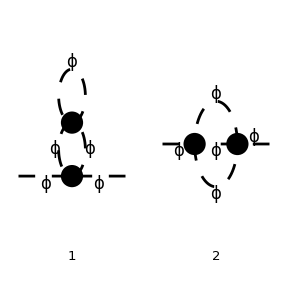

creating amplitudes at level(s) {Particles}

> Top. 1: 1 Particles amplitude

> Top. 2: 1 Particles amplitude

in total: 2 Particles amplitudes

Number of 1PI two-loop diagrams (expected 2):

2

Diagram | Momentum dependence
1 | p-independent (double scoop)
2 | depends on p (sunset)

Amplitudes in the massless limit:

{g^2/(1024 π^8 (ell_(4-e))^2 ((k_(4-e))^2)^2),g^2/(1536 π^8 (k_(4-e))^2.(ell_(4-e))^2.(ell_(4-e)+k_(4-e)+p_(4-e))^2)}

```mathematica
ClearAll[topologies2L,insertions2L,amplitudes2L,amplitudes2LFC,amplitudes2LMassless];

(*1. two-loop two-point topologies,1PI only (A-68)*)
topologies2L=CreateTopologies[2,1->1,ExcludeTopologies->{Reducible}];
(*2. insert the scalar field,same model options as Part 1*)
insertions2L=InsertFields[topologies2L,{S[1]}->{S[1]},Sequence@@phi4ModelOptions];
(*3. display*)
Paint[insertions2L,ColumnsXRows->{2,1},Numbering->Simple,SheetHeader->None];
(*4. amplitudes*)
amplitudes2L=CreateFeynAmp[insertions2L,Truncated->True];
(*5. conversion,two loop momenta.ChangeDimension->d uses the project's d=4-e,i.e.FeynCalc's D=4-2 epsFC with e=2 epsFC;no further conversion is needed*)
amplitudes2LFC=FCFAConvert[amplitudes2L,IncomingMomenta->{p},OutgoingMomenta->{p},LoopMomenta->{k,ell},ChangeDimension->d];
(*6. massless critical limit (A-69)*)
amplitudes2LMassless=amplitudes2LFC/. mphi->0;

(*7. classification:which graphs depend on p (A-68)*)
pDependentQ[amp_]:=!FreeQ[amp,p];
classification=Table[{i,If[pDependentQ[amplitudes2LMassless[[i]]],"depends on p (sunset)","p-independent (double scoop)"]},{i,Length[amplitudes2LMassless]}];
Print["Number of 1PI two-loop diagrams (expected 2):"];
Length[amplitudes2LFC]
Grid[Prepend[classification,{"Diagram","Momentum dependence"}],Frame->All]
sunsetIndex=First@Flatten@Position[pDependentQ/@amplitudes2LMassless,True];
Print["Amplitudes in the massless limit:"];
amplitudes2LMassless//FCE
```

--------------------------------------------------------------------------------------------------------------------------------------------------------------------------------

#### 2.1.2 Sunset Diagram and Its Symmetry Factor

We first determine the symmetry factor of the sunset diagram. Each of the two quartic vertices has three internal lines connecting it to the other vertex. Since these internal lines are indistinguishable, their permutations leave the diagram unchanged. There are therefore 3!=6 equivalent permutations, corresponding to the symmetry factor .

The same result can be obtained directly by counting Wick contractions at second order in the interaction expansion. The expansion contributes a factor of 1/2!, while the two quartic interaction vertices contribute . There are two ways to assign the two external legs to the vertices,  ways to select the corresponding vertex legs, and 3! ways to pair the remaining internal legs. Thus, the net combinatorial factor is

                                                                                                                                                                                                                                 (A-70)

Consequently, the sunset diagram carries a symmetry factor of , in addition to its two interaction-vertex factors.

To express its contribution, we assign independent loop momenta  and  to two of the internal propagators. Momentum conservation then fixes the momentum flowing through the third propagator to be , where  is the external Euclidean momentum. The resulting scalar integral is

                                                                                                                                                              (A-72)

Here, the factor  accounts for the dimensional-regularization scale associated with the two independent loop integrations.
With the FeynArts coupling denoted by \(g\), the converted sunset amplitude has the structure:

                                                                                                                                                                                                       (A-71)

where the two loop integration measures are understood. This agrees with the prefactor obtained from FCFAConvert in Section 2.1.1. The coupling can subsequently be identified with the interaction coupling  according to the convention established in Part 1.

The integral  is the central object in the two-loop calculation of the momentum-dependent part of the 1PI two-point function. Unlike the momentum-independent contributions, it depends on the nonzero external scale  and therefore does not vanish as a scaleless integral in dimensional regularization. In the next subsection, we evaluate it by performing two successive massless one-loop convolutions, obtaining its gamma-function representation and Laurent expansion around .

With the Euclidean interaction vertex given by , the two sunset vertices contribute a factor . Including the symmetry factor 1/6, the sunset contribution to the two-loop 1PI two-point function is therefore

                                                                                                                                                                                                                                    (A-81)

The overall minus sign follows from the two-loop expansion of , together with the convention that the tree-level Euclidean four-point vertex is .

```mathematica
ClearAll[sunsetAmplitudeMassless,sunsetAutomorphismCount,sunsetSymmetryFactor,sunsetContractionFactor,scoopContractionFactor,sunsetAmplitudePrefactor,scoopAmplitudePrefactor,sunsetPrefactorCheck,scoopPrefactorCheck,sunsetLoopMeasure,sunsetIntegrand,sunsetHIntegrand,sunsetIndex,classification,pDependentQ,momentumDependenceFlags];
```

```mathematica
(*Requires the 2.1.1 cell:amplitudes2LMassless Here p is the external Euclidean momentum vector.The scalar p2=p^2 is introduced in Section 2.1.3.*)
(*Step 1:Classify the two-loop 1PI diagrams*)
pDependentQ[amp_]:=!FreeQ[amp,p];

momentumDependenceFlags=pDependentQ/@amplitudes2LMassless;

classification=Table[{i,If[momentumDependenceFlags[[i]],"depends on p (sunset)","p-independent (double scoop)"]},{i,Length[amplitudes2LMassless]}];

sunsetPositions=Flatten@Position[momentumDependenceFlags,True];

scoopPositions=Flatten@Position[momentumDependenceFlags,False];

(*Verify that exactly one diagram of each type is present.*)

If[Length[sunsetPositions]!=1||Length[scoopPositions]!=1,Print["Error: Expected exactly one sunset and one double-scoop diagram."];
Abort[]];

sunsetIndex=First[sunsetPositions];
scoopIndex=First[scoopPositions];

Print["Number of 1PI two-loop diagrams:"];
Length[amplitudes2LMassless]

Print["Diagram classification:"];
Grid[Prepend[classification,{"Diagram","Momentum dependence"}],Frame->All]

Print["Sunset index:"];
sunsetIndex

Print["Double-scoop index:"];
scoopIndex


(* ==============================================*)
(*Step 2:Isolate the massless sunset amplitude*)
(* ==============================================*)

(*A-72*)

sunsetAmplitudeMassless=amplitudes2LMassless[[sunsetIndex]];

Print["Massless sunset amplitude:"];
sunsetAmplitudeMassless//FCE


(* ==============================================*)
(*Step 3:Derive the symmetry and contraction*)
(*factors*)
(* ==============================================*)

(*Sunset:three equivalent internal-line permutations.*)

sunsetAutomorphismCount=Factorial[3];

sunsetSymmetryFactor=1/sunsetAutomorphismCount;

(*Independent derivation from Wick contractions.*)

sunsetContractionFactor=(1/Factorial[2]) (1/Factorial[4])^2*2*(4*4)*Factorial[3];

scoopContractionFactor=(1/Factorial[2]) (1/Factorial[4])^2*2*(4*3)*(4*3)*1;

Print["Number of equivalent internal-line permutations:"];
sunsetAutomorphismCount

Print["Sunset symmetry factor:"];
sunsetSymmetryFactor

Print["Wick-contraction factor, sunset (expected: 1/6):"];
sunsetContractionFactor

Print["Wick-contraction factor, double scoop (expected: 1/4):"];
scoopContractionFactor


(* ==============================================*)
(*Step 4:Check the numerical amplitude*)
(*prefactors*)
(* ==============================================*)

(*A-72*)

sunsetAmplitudePrefactor=sunsetAmplitudeMassless/. _FeynAmpDenominator->1;

scoopAmplitudePrefactor=amplitudes2LMassless[[scoopIndex]]/.
_FeynAmpDenominator->1;

sunsetPrefactorCheck=FullSimplify[sunsetAmplitudePrefactor-g^2 sunsetSymmetryFactor/(2 Pi)^8];

scoopPrefactorCheck=FullSimplify[scoopAmplitudePrefactor-g^2 scoopContractionFactor/(2 Pi)^8];

Print["Numerical prefactor of the sunset amplitude:"];
sunsetAmplitudePrefactor//FullSimplify

Print["Sunset prefactor check (expected: 0):"];
sunsetPrefactorCheck

Print["Double-scoop prefactor check (expected: 0):"];
scoopPrefactorCheck


(* ==============================================*)
(*Step 5:Define the two-loop DR measure*)
(* ==============================================*)

(*One factor of muR^e per independent loop.*)

sunsetLoopMeasure=muR^(2 e)/(2 Pi)^(2 d);

Print["Two-loop dimensional-regularization measure:"];
sunsetLoopMeasure//TraditionalForm


(* ==============================================*)
(*Step 6:Construct the massless sunset*)
(*integrand*)
(* ==============================================*)

(*A-73*)

sunsetIntegrand=1/(SPD[k,k]*SPD[ell,ell]*SPD[k+ell+p,k+ell+p]);

sunsetHIntegrand=sunsetLoopMeasure*sunsetIntegrand;

Print["Massless sunset integrand:"];
sunsetIntegrand//FCE

Print["Sunset integrand including the two-loop measure:"];
sunsetHIntegrand//FCE


(* ==============================================*)
(*Step 7:Final consistency checks*)
(* ==============================================*)

sunsetDiagramChecks={Length[amplitudes2LMassless]==2,Length[sunsetPositions]==1,Length[scoopPositions]==1,sunsetSymmetryFactor==1/6,sunsetContractionFactor==1/6,scoopContractionFactor==1/4,FullSimplify[sunsetPrefactorCheck]==0,FullSimplify[scoopPrefactorCheck]==0,FreeQ[sunsetAmplitudeMassless,mphi],!FreeQ[sunsetIntegrand,p]};

Print["Final consistency checks (expected: all True):"];
sunsetDiagramChecks
```

Number of 1PI two-loop diagrams:

2

Diagram classification:

Diagram | Momentum dependence
1 | p-independent (double scoop)
2 | depends on p (sunset)

Sunset index:

2

Double-scoop index:

1

Massless sunset amplitude:

g^2/(1536 π^8 (k_(4-e))^2.(ell_(4-e))^2.(ell_(4-e)+k_(4-e)+p_(4-e))^2)

Number of equivalent internal-line permutations:

6

Sunset symmetry factor:

1/6

Wick-contraction factor, sunset (expected: 1/6):

1/6

Wick-contraction factor, double scoop (expected: 1/4):

1/4

Numerical prefactor of the sunset amplitude:

g^2/(1536 π^8)

Sunset prefactor check (expected: 0):

0

Double-scoop prefactor check (expected: 0):

0

Two-loop dimensional-regularization measure:

(2 π)^(-2 (4-e)) muR^(2 e)

Massless sunset integrand:

1/(ell^2 k^2 (ell+k+p)^2)

Sunset integrand including the two-loop measure:

((2 π)^(-2 (4-e)) muR^(2 e))/(ell^2 k^2 (ell+k+p)^2)

Final consistency checks (expected: all True):

{True,True,True,True,True,True,True,True,True,True}

--------------------------------------------------------------------------------------------------------------------------------------------------------------------------------

#### 2.1.3 Evaluation of the Massless Sunset Integral

We now evaluate the massless sunset integral introduced in the previous subsection

                                                                                                                     

using dimensional regularization. Since the integral depends on the nonzero external Euclidean momentum , it is not scaleless and can be evaluated by successive one-loop integrations.

The calculation relies on the standard massless one-loop convolution formula,

                                                                                                                                            (A-73)
This identity is understood by analytic continuation in the dimensional and propagator exponents, as appropriate for dimensional regularization.

We first perform the integration over , treating  as the external momentum of this one-loop subintegral. Setting , we obtain:

                                                                                                                                                    (A-74)

Substituting this result into the original expression reduces the sunset integral to a second massless one-loop convolution over . Applying the same identity with  gives the complete gamma-function representation

                                                                                                                                                                                                   (A-75)

For , this becomes:

                                                                                                                                                                                                  (A-76)

We next expand this expression as a Laurent series around . The pole originates from , while the remaining gamma functions and scale-dependent factors contribute to the finite part. The resulting expansion has the form:
     
                                                                                                                                                             (A-77)                                               

Thus, the coefficient of the momentum-dependent ultraviolet pole in the scalar sunset integral is:

                                                                                                                                                                                                                              (A-78)

This result establishes the momentum-dependent pole of the bare sunset integral. Its contribution to the complete two-point function must additionally include the sunset symmetry factor, the interaction-vertex factors, and the appropriate counterterm contributions. In the following subsection, we examine the four-point subdivergences and their counterterm insertions to establish which terms can contribute to the coefficient of .

```mathematica
ClearAll[masslessConvolutionCoefficient,masslessConvolution,sunsetFirstConvolutionCoefficient,sunsetFirstConvolution,sunsetSecondConvolutionCoefficient,sunsetSecondConvolution,sunsetGammaExact,sunsetGammaDR,sunsetPoleCoefficient,sunsetExpectedPoleCoefficient,sunsetPoleCheck,sunsetFinitePart,sunsetMomentumScalingCheck,sunsetEvaluationChecks,sunsetLaurentSeries,sunsetLaurentExpansion,convolutionD3Check,sunsetGammaExactGeneral,sunsetGammaHand,sunsetGammaFormCheck,sunsetExpectedFinitePart,sunsetFiniteCheck,sunsetDoublePoleCheck];
```

```mathematica
(*p2=p^2 (symbol).dgen is a GENERIC dimension symbol:d itself already equals 4-e (1.1.1).*)

(*Step 1:massless one-loop convolution formula (A-74):Integral d^dm q/(2 Pi)^dm 1/[(q^2)^alpha ((q+P)^2)^beta]=(P^2)^(dm/2-alpha-beta)/(4 Pi)^(dm/2) C*)
masslessConvolutionCoefficient[alpha_,beta_,dm_]:=Gamma[dm/2-alpha] Gamma[dm/2-beta] Gamma[alpha+beta-dm/2]/(Gamma[alpha] Gamma[beta] Gamma[dm-alpha-beta]);
masslessConvolution[alpha_,beta_,q2_,dm_]:=q2^(dm/2-alpha-beta)/(4 Pi)^(dm/2) masslessConvolutionCoefficient[alpha,beta,dm];

(*independent check of the formula in dm=3,where the integral is 1/(8|q|)*)
convolutionD3Check=FullSimplify[masslessConvolution[1,1,q2,3]-1/(8 Sqrt[q2]),Assumptions->q2>0];
Print["Master formula in d = 3 vs 1/(8|q|) (expected: 0):"];
convolutionD3Check

(*Step 2:first convolution,integrate over k with external momentum ell+p (A-75)*)
sunsetFirstConvolutionCoefficient=FullSimplify[masslessConvolutionCoefficient[1,1,dgen]];
sunsetFirstConvolution=FullSimplify[masslessConvolution[1,1,q2,dgen]];
Print["First convolution coefficient:"];sunsetFirstConvolutionCoefficient//TraditionalForm
Print["First convolution result:"];sunsetFirstConvolution//TraditionalForm

(*Step 3:second convolution,over ell with exponents alpha=1,beta=2-dgen/2 (A-76)*)
sunsetSecondConvolutionCoefficient=FullSimplify[masslessConvolutionCoefficient[1,2-dgen/2,dgen]];
sunsetSecondConvolution=FullSimplify[masslessConvolution[1,2-dgen/2,p2,dgen]];
Print["Second convolution coefficient:"];sunsetSecondConvolutionCoefficient//TraditionalForm
Print["Second convolution result:"];sunsetSecondConvolution//TraditionalForm

(*Step 4:exact two-loop sunset integral in generic dimension (A-77).Two loops give muR^(2 e) with e=4-dgen.*)
sunsetGammaExactGeneral=FullSimplify[muR^(2 (4-dgen))*sunsetFirstConvolutionCoefficient sunsetSecondConvolutionCoefficient*p2^(dgen-3)/(4 Pi)^dgen];
Print["Exact two-loop sunset integral, generic dimension:"];
sunsetGammaExactGeneral//TraditionalForm

(*hand-derived closed form of the product of the two convolutions*)
sunsetGammaHand=muR^(2 (4-dgen)) p2^(dgen-3) Gamma[dgen/2-1]^3 Gamma[3-dgen]/((4 Pi)^dgen Gamma[3 dgen/2-3]);
sunsetGammaFormCheck=FullSimplify[FunctionExpand[sunsetGammaExactGeneral/sunsetGammaHand-1],Assumptions->{3<dgen<4,p2>0,muR>0}];
Print["Product of convolutions vs closed gamma form (expected: 0):"];
sunsetGammaFormCheck

(*Step 5:d=4-e (A-77)*)
sunsetGammaDR=FullSimplify[sunsetGammaExactGeneral/. dgen->4-e];
Print["Sunset integral in d = 4 - e dimensions:"];
sunsetGammaDR//TraditionalForm

(*Step 6:Laurent expansion around e=0 (A-78)*)
sunsetLaurentSeries=FullSimplify[Series[sunsetGammaDR,{e,0,0}]];
Print["Sunset Laurent expansion through finite order:"];
sunsetLaurentSeries//TraditionalForm

(*Step 7:coefficient of p^2/e (A-79)*)
sunsetPoleCoefficient=FullSimplify[SeriesCoefficient[sunsetGammaDR,{e,0,-1}]];
sunsetExpectedPoleCoefficient=-p2/(2 (4 Pi)^4);
sunsetPoleCheck=FullSimplify[sunsetPoleCoefficient-sunsetExpectedPoleCoefficient];
Print["Coefficient of the 1/e pole:"];sunsetPoleCoefficient//TraditionalForm
Print["Pole coefficient check (expected: 0):"];sunsetPoleCheck

(*Step 8:finite part against the hand-derived value (A-78)*)
sunsetFinitePart=FullSimplify[SeriesCoefficient[sunsetGammaDR,{e,0,0}]];
sunsetExpectedFinitePart=p2 (Log[p2]-2 Log[muR]-Log[4 Pi]+EulerGamma-13/4)/(512 Pi^4);
sunsetFiniteCheck=FullSimplify[sunsetFinitePart-sunsetExpectedFinitePart,Assumptions->{p2>0,muR>0}];
Print["Finite part of the sunset integral:"];sunsetFinitePart//TraditionalForm
Print["Finite part check (expected: 0):"];sunsetFiniteCheck

(*Step 9:momentum scaling of the pole and absence of a 1/e^2 pole*)
sunsetMomentumScalingCheck=FullSimplify[sunsetPoleCoefficient/p2];
sunsetDoublePoleCheck=FullSimplify[SeriesCoefficient[sunsetGammaDR,{e,0,-2}]];
Print["Pole coefficient divided by p^2:"];sunsetMomentumScalingCheck//TraditionalForm
Print["Coefficient of 1/e^2 (expected: 0):"];sunsetDoublePoleCheck

(*Step 10:final checks*)
sunsetEvaluationChecks={convolutionD3Check==0,sunsetGammaFormCheck==0,sunsetPoleCheck==0,sunsetFiniteCheck==0,FullSimplify[sunsetMomentumScalingCheck+1/(2 (4 Pi)^4)]==0,sunsetDoublePoleCheck==0};
Print["Final sunset evaluation checks (expected: all True):"];
sunsetEvaluationChecks
```

Master formula in d = 3 vs 1/(8|q|) (expected: 0):

0

First convolution coefficient:

-(π csc((π dgen)/2) dgen/2-1)/(dgen-2)

First convolution result:

-(2^(3-2 dgen) π^(3/2-dgen/2) q2^(dgen/2-2) csc((π dgen)/2))/((dgen-1)/2)

Second convolution coefficient:

(π csc(π dgen) dgen/2-1)/(2-dgen/2 (3 dgen)/2-3)

Second convolution result:

(2^-dgen π^(1-dgen/2) p2^(dgen-3) csc(π dgen) dgen/2-1)/(2-dgen/2 (3 dgen)/2-3)

Exact two-loop sunset integral, generic dimension:

-(π^2 (4 π)^-dgen muR^(8-2 dgen) p2^(dgen-3) csc((π dgen)/2) csc(π dgen) (dgen/2-1)^2)/(2-dgen/2 dgen-2 (3 dgen)/2-3)

Product of convolutions vs closed gamma form (expected: 0):

0

Sunset integral in d = 4 - e dimensions:

-(4^(e-4) π^(e-2) muR^(2 e) p2^(1-e) csc((π e)/2) csc(π e) (1-e/2)^2)/(3-(3 e)/2 2-e e/2)

Sunset Laurent expansion through finite order:

-p2/(512 π^4 e)+(p2 (-8 log(muR)+4 log(p2)+4 ℽ-13-4 log(4 π)))/(2048 π^4)+O(e^1)

Coefficient of the 1/e pole:

-p2/(512 π^4)

Pole coefficient check (expected: 0):

0

Finite part of the sunset integral:

(p2 (-8 log(muR)+4 log(p2)+4 ℽ-13-4 log(4 π)))/(2048 π^4)

Finite part check (expected: 0):

0

Pole coefficient divided by p^2:

-1/(512 π^4)

Coefficient of 1/e^2 (expected: 0):

0

Final sunset evaluation checks (expected: all True):

{True,True,True,True,True,True}

--------------------------------------------------------------------------------------------------------------------------------------------------------------------------------

#### 2.1.4 Four-Point Subdivergences and the Momentum-Dependent Pole

The two-loop sunset diagram contains logarithmically divergent four-point subgraphs. Each such subgraph is obtained by selecting two of the three internal propagators connecting the quartic vertices. The sunset contains three one-loop four-point subgraphs, one for each choice of two of its three internal lines. Each is a bubble whose four external legs are the two external lines of the diagram and the two ends of the third (spectator) line. Contracting it to a point leaves the spectator line closed on itself, i.e. a massless tadpole with a δλ vertex. The three choices are equivalent, and the single counterterm diagram with the full δλ (which already sums the three channels of Γ⁽⁴⁾) cancels all three subdivergences. (A-79)These subdivergences must be removed by inserting the corresponding coupling counterterm, , in accordance with the forest subtraction procedure.

After replacing a divergent four-point subgraph by its local counterterm, the resulting two-point contribution has the structure of a massless one-loop tadpole:

                                                                                                                                                         

This integral contains no external momentum . In massless dimensional regularization, it is scaleless and therefore vanishes. The vanishing of the massless tadpole in DR means its UV and IR poles cancel. This does not affect the UV argument. The sunset has no IR divergence for p.b2 > 0, and the absence of a 1/ε.b2 pole in H confirms the cancellation. (A-80)
More generally, its momentum independence means that it cannot contribute to the coefficient of , although mass renormalization must still be treated consistently when imposing the criticality condition. Thus, the four-point counterterm insertions cancel the subdivergences but do not modify the momentum-dependent ultraviolet pole of the sunset integral.

Using the result obtained in Section 2.1.3,  we identify the coefficient of the momentum-dependent pole as:

                                                                                                                                 

This is the pole of the scalar sunset integral itself. The corresponding contribution to the two-point function must additionally include the sunset symmetry factor and the appropriate vertex factors, with signs fixed by the Euclidean Feynman-rule conventions established in Part 1. The absence of a -dependent contribution from the four-point counterterm insertions ensures that this pole determines the two-loop field-strength renormalization.

```mathematica
(*Step 1:momentum-dependent pole of the sunset integral (A-79)*)sunsetPolePart=FullSimplify[SeriesCoefficient[sunsetGammaDR,{e,0,-1}]];
sunsetExpectedPole=-p2/(2 (4 Pi)^4);
polePartCheck=FullSimplify[sunsetPolePart-sunsetExpectedPole];

(*Step 2:coefficient of p^2/e*)
sunsetP2PoleCoefficient=FullSimplify[sunsetPolePart/p2];
sunsetExpectedP2PoleCoefficient=-1/(2 (4 Pi)^4);
p2PoleCoefficientCheck=FullSimplify[sunsetP2PoleCoefficient-sunsetExpectedP2PoleCoefficient];

(*Step 3:no 1/e^2 pole:consistent with the vanishing counterterm tadpole below (A-81)*)
sunsetDoublePoleCoefficient=FullSimplify[SeriesCoefficient[sunsetGammaDR,{e,0,-2}]];

(*Step 4:the four-point counterterm insertion is a massless tadpole (A-80,A-81).Its integrand has no p,and the integral is the m2->0 limit of the exact DR tadpole of 1.2.3,which vanishes for 0<e<2 (scaleless integral).*)
masslessTadpoleIntegrand=1/SPD[k,k];
counterterm2PtIsPIndependent=FreeQ[masslessTadpoleIntegrand,p];
masslessTadpoleDR=Limit[TDR[m2],m2->0,Assumptions->{0<e<2,muR>0}];

(*counterterm-diagram contribution (delta lam/2) x tadpole:zero for any delta lam*)
counterterm2PtContribution=FullSimplify[(dLamMS/2) masslessTadpoleDR];

(*Step 5:two-loop sunset contribution to the Euclidean Gamma2 (A-82):Gamma2 contains-(lam^2/6) H(p),from the vertex-lam,the symmetry factor 1/6,and Gamma=tree-diagrams*)
sunsetGamma2Contribution=-(lam^2/6) sunsetGammaDR;
sunsetGamma2Pole=FullSimplify[SeriesCoefficient[sunsetGamma2Contribution,{e,0,-1}]];
sunsetGamma2PoleCheck=FullSimplify[sunsetGamma2Pole-lam^2 p2/(3072 Pi^4)];
sunsetGamma2PoleInG=FullSimplify[sunsetGamma2Pole/. lam->16 Pi^2 g];   (*expected g^2 p2/12*)

(*Step 6:collect the checks*)
subdivergenceChecks={polePartCheck==0,p2PoleCoefficientCheck==0,sunsetDoublePoleCoefficient==0,counterterm2PtIsPIndependent,masslessTadpoleDR==0,counterterm2PtContribution==0,sunsetGamma2PoleCheck==0};

Print["Sunset pole:"];sunsetPolePart
Print["Coefficient of p^2/epsilon:"];sunsetP2PoleCoefficient
Print["Coefficient of 1/e^2 (expected: 0):"];sunsetDoublePoleCoefficient
Print["Massless counterterm tadpole in DR (expected 0):"];masslessTadpoleDR
Print["Counterterm-insertion contribution (expected 0):"];counterterm2PtContribution
Print["Pole of the sunset contribution to Gamma2 (expected lam^2 p2/(3072 Pi^4)):"];
sunsetGamma2Pole
Print["Same pole in terms of g (expected g^2 p2/12):"];sunsetGamma2PoleInG
Print["Four-point subdivergence checks (expected: all True):"];
subdivergenceChecks
```

Sunset pole:

-p2/(512 π^4)

Coefficient of p^2/epsilon:

-1/(512 π^4)

Coefficient of 1/e^2 (expected: 0):

0

Massless counterterm tadpole in DR (expected 0):

0

Counterterm-insertion contribution (expected 0):

0

Pole of the sunset contribution to Gamma2 (expected lam^2 p2/(3072 Pi^4)):

(lam^2 p2)/(3072 π^4)

Same pole in terms of g (expected g^2 p2/12):

(g^2 p2)/12

Four-point subdivergence checks (expected: all True):

{True,True,True,True,True,True,True}

#### Section 2.1—Verification Summary

Question:
Which two-loop graphs are 1PI, what is the sunset’s p.b2 pole, and why do subdivergence counterterms not affect it?
------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------                                           
Derivation: 
Sections 2.1.1–2.1.4.
------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------   
Check: 
The prefactor checks, sunsetPoleCheck, sunsetDoublePoleCheck, masslessTadpoleDR.
------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------   
Anchor IDs: 
A-68 to A-81.
------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------   
Status: 
Checked!

### 2.2 Field renormalization and the anomalous dimension

In this section, we use the momentum - dependent ultraviolet divergence of the two - loop sunset diagram to determine the field - strength renormalization and the anomalous dimension of the scalar field . In Section 2.2 .1, we incorporate the sunset contribution into the inverse propagator, keeping track of its sign and symmetry factor, and isolate the divergence proportional to  . In Section 2.2 .2, we introduce the field renormalization constant  and determine the corresponding counterterm by requiring the cancellation of this divergence . In Section 2.2 .3, we derive the anomalous dimension  from the renormalization - scale dependence of , with the bare parameters held fixed . Finally, in Section 2.2 .4, we evaluate the critical exponent  at the Wilson–Fisher fixed point through order  and check the result against the finite logarithmic dependence on  obtained from the sunset integral . We also explain why the one - loop expression for the fixed-point coupling is sufficient at this order.

#### 2.2.1 Sunset Contribution to the Inverse Propagator

The only nonvanishing momentum-dependent two-loop 1PI diagram identified in Section 2.1 is the sunset diagram. Its contribution to the inverse propagator is determined by the scalar integral H(p), evaluated in Section 2.1.3, together with the diagram’s symmetry factor and the Euclidean interaction-vertex factors. 
The full propagator is , where  is the sum of the amputated 1PI diagrams, including their vertex factors. Hence , so . For the sunset, , which gives . (A-81)
The factor 1/3! is the symmetry factor from permuting the three identical internal lines connecting the two vertices.

Using the result derived in Section 2.1.3,

                                                                                                                                     (A-82)

the sunset contribution becomes:

                                                                                                                             (A-83)

In particular, the ultraviolet pole proportional to the external momentum is:

                                                                                                                             

This term is important because, unlike the one-loop tadpole, the sunset diagram depends nontrivially on the external momentum. It therefore contributes to the renormalization of the coefficient of , and hence to the field-strength renormalization constant . The momentum-independent part of the two-point function instead contributes to mass renormalization. In the following subsection, we account for the four-point subdivergences and determine their effect on the momentum-dependent pole before extracting the two-loop field anomalous dimension.

```mathematica
(*Conventions:d=4-e,p2=p^2,g=lam/(16 Pi^2).*)(*---Step 1:identify the sunset contribution from Section 2.1.4---*)sunsetInversePropagatorContribution=FullSimplify[sunsetGamma2Contribution];

sunsetContributionDefinitionCheck=FullSimplify[sunsetInversePropagatorContribution+(lam^2/6) sunsetGammaDR];


(*---Step 2:Laurent expansion through finite order---*)

sunsetInversePropagatorLaurentSeries=FullSimplify[Series[sunsetInversePropagatorContribution,{e,0,0}]];

sunsetInversePropagatorLaurentExpansion=FullSimplify[Normal[sunsetInversePropagatorLaurentSeries]];


(*---Step 3:extract the momentum-dependent UV pole---*)

sunsetInversePropagatorPole=FullSimplify[SeriesCoefficient[sunsetInversePropagatorContribution,{e,0,-1}]];

sunsetExpectedInversePropagatorPole=lam^2 p2/(12 (4 Pi)^4);

sunsetInversePropagatorPoleCheck=FullSimplify[sunsetInversePropagatorPole-sunsetExpectedInversePropagatorPole];


(*---Step 4:express the pole in terms of the normalized coupling---*)

sunsetInversePropagatorPoleInG=FullSimplify[sunsetInversePropagatorPole/. lam->16 Pi^2 g];

sunsetExpectedInversePropagatorPoleInG=g^2 p2/12;

sunsetInversePropagatorPoleInGCheck=FullSimplify[sunsetInversePropagatorPoleInG-sunsetExpectedInversePropagatorPoleInG];


(*---Step 5:extract the finite contribution---*)

sunsetInversePropagatorFinitePart=FullSimplify[SeriesCoefficient[sunsetInversePropagatorContribution,{e,0,0}]];

(*---Step 5b:finite part with the dimensionless logarithm---*)sunsetFiniteInG=sunsetInversePropagatorFinitePart/. lam->16 Pi^2 g;
sunsetFiniteExpected=(g^2 p2/12) (-Log[p2/muR^2]-EulerGamma+Log[4 Pi]+13/4);
sunsetFiniteFormCheck=FullSimplify[PowerExpand[sunsetFiniteInG-sunsetFiniteExpected]];
Print["Finite part check (expected: 0):"];sunsetFiniteFormCheck

(*---Step 6:verify the momentum dependence and pole structure---*)

sunsetInversePropagatorP2Coefficient=FullSimplify[sunsetInversePropagatorPole/p2];

sunsetInversePropagatorDoublePole=FullSimplify[SeriesCoefficient[sunsetInversePropagatorContribution,{e,0,-2}]];


(*---Step 7:display the results---*)

Print["Sunset contribution to the inverse propagator:"];
sunsetInversePropagatorContribution//TraditionalForm

Print["Laurent expansion through finite order:"];
sunsetInversePropagatorLaurentSeries//TraditionalForm

Print["Coefficient of the 1/e pole:"];
sunsetInversePropagatorPole//TraditionalForm

Print["Same pole in terms of the normalized coupling g:"];
sunsetInversePropagatorPoleInG//TraditionalForm

Print["Finite contribution:"];
sunsetInversePropagatorFinitePart//TraditionalForm

Print["Coefficient of p^2/e:"];
sunsetInversePropagatorP2Coefficient//TraditionalForm

Print["Coefficient of 1/e^2 (expected: 0):"];
sunsetInversePropagatorDoublePole//TraditionalForm


(*---Step 8:final consistency checks---*)

sunsetInversePropagatorChecks={sunsetContributionDefinitionCheck==0,sunsetInversePropagatorPoleCheck==0,sunsetInversePropagatorPoleInGCheck==0,FullSimplify[sunsetInversePropagatorP2Coefficient-lam^2/(12 (4 Pi)^4)]==0,sunsetInversePropagatorDoublePole==0,sunsetFiniteFormCheck==0};

Print["Final consistency checks (expected: all True):"];
sunsetInversePropagatorChecks
```

Finite part check (expected: 0):

0

Sunset contribution to the inverse propagator:

(2^(2 e-9) π^(e-2) lam^2 muR^(2 e) p2^(1-e) csc((π e)/2) csc(π e) (1-e/2)^2)/(3 3-(3 e)/2 2-e e/2)

Laurent expansion through finite order:

(lam^2 p2)/(3072 π^4 e)+(lam^2 p2 (8 log(2 muR)-4 log(p2)-4 ℽ+13+4 log(π)))/(12288 π^4)+O(e^1)

Coefficient of the 1/e pole:

(lam^2 p2)/(3072 π^4)

Same pole in terms of the normalized coupling g:

(g^2 p2)/12

Finite contribution:

(lam^2 p2 (8 log(muR)-4 log(p2)-4 ℽ+13+4 log(π)+log(256)))/(12288 π^4)

Coefficient of p^2/e:

lam^2/(3072 π^4)

Coefficient of 1/e^2 (expected: 0):

0

Final consistency checks (expected: all True):

{True,True,True,True,True,True}

#### 2.2.2 Field-Strength Renormalization

The momentum-dependent ultraviolet divergence obtained from the sunset diagram in Section 2.2.1 requires a field-strength counterterm. To determine this counterterm, we introduce the field renormalization constant , relating the bare and renormalized fields through

                                                                                                                                                                                                                                   (A-85)

The corresponding contribution to the inverse propagator is . Since the one-loop tadpole is independent of the external momentum, it does not contribute to field-strength renormalization. At two-loop order, the sunset diagram generates the momentum-dependent pole:

                                                                                                                              

where  is the normalized coupling defined in Part 1. Minimal subtraction requires the field-strength counterterm to cancel this divergence. Thus, writing  we obtain:

                                                                                                                                                                                                 (A-87)

The negative sign is essential: the counterterm enters the inverse propagator with a positive contribution , and must therefore cancel the positive sunset pole. The only other two-loop topology is the tadpole with a  counterterm inserted on the bubble. It has no dependence on the external momentum p, so it can renormalize only the mass and cannot touch the  pole. Independently, at  it is a scaleless integral, , so it vanishes identically in dimensional regularization. (A-86)

Having determined , we can now calculate the field anomalous dimension. It is defined at fixed bare parameters by

                                                                                                                                         

The derivative must be evaluated using the  beta function, including its canonical  contribution. We will use this relation in the next subsection to obtain the two-loop anomalous dimension and evaluate it at the Wilson–Fisher fixed point.

```mathematica
(*Conventions:d=4-e,g=lam/(16 Pi^2).*)
(*---Step 1:one-loop field-strength counterterm---*)
(*The one-loop tadpole is momentum independent.*)
deltaZPhi1=0;


(*---Step 2:extract the two-loop sunset pole in terms of g---*)

sunsetFieldStrengthPole=FullSimplify[sunsetInversePropagatorPoleInG/p2];

sunsetExpectedFieldStrengthPole=g^2/12;

sunsetFieldStrengthPoleCheck=FullSimplify[sunsetFieldStrengthPole-sunsetExpectedFieldStrengthPole];


(*---Step 3:determine the MS field-strength counterterm---*)

(*The counterterm must cancel the p^2/e pole.*)
deltaZPhi2=FullSimplify[-sunsetFieldStrengthPole/e];

deltaZPhiMS=FullSimplify[deltaZPhi1+deltaZPhi2];

ZphiMS=FullSimplify[1+deltaZPhiMS];

pureMSCheck=FreeQ[deltaZPhiMS,EulerGamma|Log[_]|Pi];


(*---Step 4:verify cancellation of the momentum-dependent pole---*)

sunsetPoleContribution=sunsetInversePropagatorPoleInG/e;

fieldStrengthCountertermContribution=FullSimplify[deltaZPhiMS*p2];

totalMomentumDependentPole=FullSimplify[sunsetPoleContribution+fieldStrengthCountertermContribution];

fieldStrengthCancellationCheck=FullSimplify[totalMomentumDependentPole];


(*---Step 5:verify the absence of a one-loop contribution---*)

oneLoopFieldStrengthCheck=FullSimplify[deltaZPhi1];


(*---Step 6:verify that the four-point subdivergence does not contribute to field-strength renormalization---*)

(*---Step 6:four-point subdivergence insertion---*)subdivergenceP2Dependence=FullSimplify[D[counterterm2PtContribution,p2]];
scalelessTadpole=Limit[m^(2-e) Gamma[-1+e/2],m->0,Assumptions->0<e<2];
fourPointSubdivergenceCheck={subdivergenceP2Dependence==0,scalelessTadpole==0};


(*---Step 7:display the results---*)

Print["One-loop field-strength counterterm:"];
deltaZPhi1//TraditionalForm

Print["Two-loop sunset pole coefficient (in terms of g):"];
sunsetFieldStrengthPole//TraditionalForm

Print["Two-loop MS field-strength counterterm:"];
deltaZPhi2//TraditionalForm

Print["Total MS field-strength counterterm:"];
deltaZPhiMS//TraditionalForm

Print["Field-strength renormalization constant Z_phi:"];
ZphiMS//TraditionalForm

Print["Total momentum-dependent pole after counterterm insertion:"];
totalMomentumDependentPole//TraditionalForm

Print["Subdivergence insertion: p^2-independence and scalelessness (expected: {True, True}):"];
fourPointSubdivergenceCheck

(*---Step 8:final consistency checks---*)

fieldStrengthRenormalizationChecks={sunsetFieldStrengthPoleCheck==0,deltaZPhi1==0,FullSimplify[deltaZPhi2+g^2/(12 e)]==0,FullSimplify[ZphiMS-(1-g^2/(12 e))]==0,fieldStrengthCancellationCheck==0,And@@fourPointSubdivergenceCheck};

Print["Final field-strength renormalization checks (expected: all True):"];
fieldStrengthRenormalizationChecks
```

One-loop field-strength counterterm:

0

Two-loop sunset pole coefficient (in terms of g):

g^2/12

Two-loop MS field-strength counterterm:

-g^2/(12 e)

Total MS field-strength counterterm:

-g^2/(12 e)

Field-strength renormalization constant Z_phi:

1-g^2/(12 e)

Total momentum-dependent pole after counterterm insertion:

0

Subdivergence insertion: p^2-independence and scalelessness (expected: {True, True}):

{True,True}

Final field-strength renormalization checks (expected: all True):

{True,True,True,True,True,True}

#### 2.2.3 Anomalous Dimension

Having determined the field-strength renormalization constant in Section 2.2.2, we now calculate the field anomalous dimension. It is defined by the renormalization-scale dependence of  at fixed bare parameters:

                                                                                                                

where the d-dimensional beta function is:

                                                                                                                                                                                                      (A-88)

From Section 2.2.2, the field-strength renormalization constant in the minimal-subtraction scheme is  Substituting this expression into the definition of  (A-89), and retaining terms through order , gives:

                                                                                                               (A-90)
Thus, the two-loop field anomalous dimension is:

                                                                                                                      

The explicit  pole cancels at , which is the order computed here. The  term is cancelled by the double-pole part of , which lies beyond the order of this calculation. Finiteness holds order by order in , not for the truncated  at fixed .

Finally, using the Wilson–Fisher fixed point obtained in Part 1,  we can evaluate the anomalous dimension at criticality. This fixed-point value will determine the critical exponent  in the next subsection.

```mathematica
(*Conventions:d=4-e,g=lam/(16 Pi^2).*)
(*---Step 1:define the d-dimensional beta function---*)
betaGDimensionallyContinued=FullSimplify[betaD];


(*---Step 2:define the field anomalous dimension---*)

(*gamma_phi=(1/2) beta_g d[Log[Z_phi]]/dg,with the bare parameters held fixed.*)

gammaPhiExact=FullSimplify[1/2 betaGDimensionallyContinued D[Log[ZphiMS],g]];


(*---Step 3:expand through two-loop order---*)

gammaPhiSeries=FullSimplify[Series[gammaPhiExact,{g,0,2}]];

gammaPhi=FullSimplify[Normal[gammaPhiSeries]];


(*---Step 4:extract the two-loop coefficient---*)

gammaPhiTwoLoopCoefficient=FullSimplify[SeriesCoefficient[gammaPhi,{g,0,2}]];

gammaPhiExpected=g^2/12;

gammaPhiCoefficientCheck=FullSimplify[gammaPhi-gammaPhiExpected];


(*---Step 5:pole structure order by order in g---*)gammaPhiCoefficients=Table[FullSimplify[SeriesCoefficient[gammaPhiExact,{g,0,n}]],{n,1,3}];
gammaPhiPoleCheck=FullSimplify[gammaPhiCoefficients-{0,1/12,-1/(4 e)}];
gammaPhiFiniteAtTwoLoops=FreeQ[gammaPhiCoefficients[[2]],e];


(*---Step 6:display the results---*)

Print["Dimensionally continued beta function:"];
betaGDimensionallyContinued//TraditionalForm

Print["Exact anomalous-dimension expression:"];
gammaPhiExact//TraditionalForm

Print["Anomalous dimension through O(g^2):"];
gammaPhi//TraditionalForm

Print["Two-loop coefficient:"];
gammaPhiTwoLoopCoefficient//TraditionalForm

Print["Coefficients of g, g^2, g^3 (expected: 0, 1/12, -1/(4e)):"];
gammaPhiCoefficients//TraditionalForm


(*---Step 7:final consistency checks---*)anomalousDimensionChecks={FullSimplify[betaGDimensionallyContinued-(-e g+3 g^2)]==0,FullSimplify[gammaPhi-g^2/12]==0,FullSimplify[gammaPhiTwoLoopCoefficient-1/12]==0,gammaPhiPoleCheck=={0,0,0},gammaPhiFiniteAtTwoLoops};

Print["Final anomalous-dimension checks (expected: all True):"];
anomalousDimensionChecks
```

Dimensionally continued beta function:

g (3 g-e)

Exact anomalous-dimension expression:

(g^2 (e-3 g))/(12 e-g^2)

Anomalous dimension through O(g^2):

g^2/12

Two-loop coefficient:

1/12

Coefficients of g, g^2, g^3 (expected: 0, 1/12, -1/(4e)):

{0,1/12,-1/(4 e)}

Final anomalous-dimension checks (expected: all True):

{True,True,True,True,True}

#### 2.2.4 Critical Exponent and Logarithmic Consistency Check

We now evaluate the field anomalous dimension at the Wilson–Fisher fixed point to obtain the critical exponent . The anomalous dimension modifies the scaling of the critical two-point function according to  where, with our convention for the field anomalous dimension, 
Using the two-loop result from Section 2.2.3,  and the Wilson–Fisher fixed point obtained in Part 1, (A-91) we find:

                                                                                                                =                                                                                                         (A-92)

Therefore, the anomalous critical exponent is:

                                                                                                                                        

Since  starts at , we have . The two-loop beta function  shifts the fixed point to . Inserting this into  changes  only at , and the  term of  also contributes only at . Hence the one-loop  is sufficient for  through .

As an independent consistency check, we examine the logarithmic momentum dependence of the renormalized two-point function. Expanding the factor that governs the critical scaling,  and retaining terms through , gives:

                                                                                                                                                                                                                            (A-93)

Thus, the coefficient of the logarithmic momentum dependence must agree with . Since  first appears at order , this provides a useful check of the two-loop momentum-dependent contribution and its field-strength renormalization. The counterterm  is a polynomial in , so it cannot change the coefficient of . The logarithm therefore comes entirely from the finite part of the sunset, and its coefficient is fixed by the pole through the scaling  of the two-loop integral. (A-94)
This agreement provides an independent consistency check between the renormalization-group calculation and the momentum-space scaling form of the critical propagator.

```mathematica
(*Conventions:d=4-e,g=lam/(16 Pi^2).*)(*---Step 1:Wilson-Fisher fixed point---*)
gStarWF=First[DeleteCases[g/. Solve[betaD==0,g],0]];

fixedPointCheck=FullSimplify[(betaD/. g->gStarWF)];


(*---Step 2:anomalous dimension at the fixed point---*)

gammaPhiAtFixedPoint=FullSimplify[gammaPhi/. g->gStarWF];

gammaPhiFixedPointSeries=FullSimplify[Normal[Series[gammaPhiAtFixedPoint,{e,0,2}]]];


(*---Step 3:calculate eta=2 gamma_phi---*)

eta=FullSimplify[2 gammaPhiFixedPointSeries];

etaExpected=e^2/54;

etaCheck=FullSimplify[eta-etaExpected];


(*---Step 4:extract the logarithmic coefficient from the finite sunset contribution---*)

sunsetFinitePartInG=FullSimplify[sunsetInversePropagatorFinitePart/. lam->16 Pi^2 g];

sunsetFinitePartPerP2=FullSimplify[sunsetFinitePartInG/p2];

sunsetLogCoefficient=FullSimplify[Coefficient[Collect[sunsetFinitePartPerP2,Log[p2]],Log[p2]]];

(*The sunset contribution enters Gamma^(2).The corresponding correction to the propagator has the opposite sign at first order.*)

propagatorLogCoefficient=FullSimplify[-sunsetLogCoefficient];


(*---Step 5:compare the logarithmic coefficient with gamma_phi and eta---*)

expectedPropagatorLogCoefficient=FullSimplify[gammaPhi];

logarithmicCoefficientCheck=FullSimplify[propagatorLogCoefficient-expectedPropagatorLogCoefficient];

propagatorLogCoefficientAtFixedPoint=FullSimplify[propagatorLogCoefficient/. g->gStarWF];

etaFromLogarithm=FullSimplify[2 propagatorLogCoefficientAtFixedPoint];

logarithmicEtaCheck=FullSimplify[etaFromLogarithm-eta];

(*---Step 5b:structural check of the logarithm---*)(*two loops scale as (muR^2/p^2)^e,so a pole c/e comes with-c Log[p2/muR^2]*)
structuralLogCoefficient=-sunsetFieldStrengthPole;
structuralLogCheck=FullSimplify[sunsetLogCoefficient-structuralLogCoefficient];
(*mu-independence:with p2=s muR^2 no muR may remain*)
muIndependenceCheck=FreeQ[FullSimplify[PowerExpand[sunsetFinitePartPerP2/. p2->s muR^2],Assumptions->{s>0,muR>0}],muR];

(*Step 6*)
criticalPropagatorScaling=(1/p2) (p2/muR^2)^(eta/2);
criticalPropagatorLogExpansion=FullSimplify[Normal[Series[criticalPropagatorScaling p2,{e,0,2}]]/p2];


(*---Step 7:display the results---*)

Print["Wilson-Fisher fixed point:"];
gStarWF//TraditionalForm

Print["Fixed-point beta-function check (expected: 0):"];
fixedPointCheck//TraditionalForm

Print["Anomalous dimension at the fixed point:"];
gammaPhiFixedPointSeries//TraditionalForm

Print["Critical exponent eta:"];
eta//TraditionalForm

Print["Coefficient of Log[p2] in the sunset contribution to Gamma^(2):"];
sunsetLogCoefficient//TraditionalForm

Print["Coefficient of Log[p2] in the propagator correction:"];
propagatorLogCoefficient//TraditionalForm

Print["Eta obtained from the logarithmic coefficient:"];
etaFromLogarithm//TraditionalForm

Print["Critical propagator scaling:"];
criticalPropagatorScaling//TraditionalForm

Print["Expansion of the critical propagator through O(e^2):"];
criticalPropagatorLogExpansion//TraditionalForm


(*---Step 8:final consistency checks---*)

criticalExponentChecks={fixedPointCheck==0,FullSimplify[etaCheck]==0,FullSimplify[gammaPhiFixedPointSeries-e^2/108]==0,FullSimplify[logarithmicCoefficientCheck]==0,FullSimplify[logarithmicEtaCheck]==0,FullSimplify[propagatorLogCoefficientAtFixedPoint-e^2/108]==0,structuralLogCheck==0,muIndependenceCheck};

Print["Final critical-exponent checks (expected: all True):"];
criticalExponentChecks
```

Wilson-Fisher fixed point:

e/3

Fixed-point beta-function check (expected: 0):

0

Anomalous dimension at the fixed point:

e^2/108

Critical exponent eta:

e^2/54

Coefficient of Log[p2] in the sunset contribution to Gamma^(2):

-g^2/12

Coefficient of Log[p2] in the propagator correction:

g^2/12

Eta obtained from the logarithmic coefficient:

e^2/54

Critical propagator scaling:

((p2/muR^2)^(e^2/108))/p2

Expansion of the critical propagator through O(e^2):

(1/108 e^2 log(p2/muR^2)+1)/p2

Final critical-exponent checks (expected: all True):

{True,True,True,True,True,True,True,True}

#### Section 2.2—Verification Summary

Question:
How does the two-loop field-strength renormalization determine the anomalous dimension  and the critical exponent  through ,
 and how can the result be independently verified from the logarithmic momentum dependence of the critical propagator?
------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------                                           
Derivation: 
Sections 2.2.1 to 2.2.4.
------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------   
Check: 
The two-loop sunset pole determines , yielding the finite anomalous dimension . Evaluating at 
the Wilson–Fisher fixed point gives . The logarithmic coefficient in the renormalized critical propagator agrees with , 
providing an independent consistency check.
------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------   
Anchor IDs: 
A-82 to A-94
------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------   
Status: 
Checked!

### 2.3 Scaling and comparison with water

In this section, we derive the critical-isotherm exponent  from the scaling dimensions of the scalar field and its conjugate external source. In Section 2.3.1, we introduce a uniform external field , define the order parameter , and derive the scaling dimensions of both quantities to establish the scaling relation for . In Section 2.3.2, we use this relation together with the two-loop anomalous dimension obtained in Section 2.2 to calculate  through  and obtain its three-dimensional prediction by setting . In Section 2.3.3, we connect the field-theoretic critical isotherm to the experimentally measurable equation of state of water by identifying the order parameter and external field with the density and pressure deviations from their critical values. Finally, in Section 2.3.4, we derive the critical scattering exponent from the momentum-space scaling of the two-point function and compare our predictions for  and  with the experimental water-fit and conformal-bootstrap reference values.

#### 2.3.1 External Field and Scaling Dimensions

To derive the critical-isotherm exponent , we introduce a uniform external source  coupled linearly to the scalar field through

                                                                                                                                                                                                                                            (A-95)
 
The order parameter is defined as the expectation value of the field in the presence of this source,  With Euclidean weight , this is . The critical isotherm means , that is, the mass is tuned to criticality as in Part 2.

At criticality, the scaling dimension of the scalar field is:

                                                                                                                                                                                                                                                          (A-96)

where  is the exponent obtained in Section 2.2.4, so that . This agrees with , whose Fourier transform is the  of Section 2.2.4. Since the source term must remain dimensionless under a scale transformation, the scaling dimension of the external field is determined by  giving

                                                                                                                                                                                                                                            (A-97)

Under a common rescaling by a factor , the source and the order parameter transform as  and , with the same sign convention for both. The combination  is therefore invariant, so the equation of state must have the form . Equivalently, the critical-isotherm equation takes the form , with

                                                                                                                                                                                                                                                  (A-98)

This scaling relation allows us to determine  directly from the anomalous dimension calculated in Section 2.2, without requiring an additional perturbative calculation of the equation of state. The relation assumes hyperscaling and a single relevant field at ; it is a scaling argument, not an independent perturbative calculation of the equation of state.

```mathematica
(*Conventions:dim=spacetime dimension,anomEta=generic anomalous-dimension exponent.*)
(*---1. Define scaling dimensions---*)
deltaPhi=(dim-2+anomEta)/2;
deltaH=dim-deltaPhi;

(*---2. Verify the source-term scaling relation Delta_h+Delta_phi=d---*)
sourceScalingCheck=FullSimplify[deltaH+deltaPhi-dim];
deltaHExpectedCheck=FullSimplify[deltaH-(dim+2-anomEta)/2];

(*---3. Derive the critical-isotherm exponent delta=Delta_h/Delta_phi---*)
deltaScalingRelation=FullSimplify[deltaH/deltaPhi];
deltaExpected=(dim+2-anomEta)/(dim-2+anomEta);
deltaScalingCheck=FullSimplify[deltaScalingRelation-deltaExpected];

(*---4. Invariance of h^Delta_phi/M^Delta_h under the common rescaling by b---*)
orderParameterScaling=b^(-deltaPhi);
externalFieldScaling=b^(-deltaH);
criticalIsothermScalingCheck=FullSimplify[PowerExpand[(externalFieldScaling)^deltaPhi/(orderParameterScaling)^deltaH],Assumptions->b>0];

(*---5. Bridge to Section 2.2.4:d=4-e and eta from the two-loop calculation---*)
deltaBridge=FullSimplify[deltaScalingRelation/. {dim->4-e,anomEta->eta}];
deltaBridgeCheck=FullSimplify[deltaBridge-(6-e-e^2/54)/(2-e+e^2/54)];

(*---6. Final consistency checks---*)
scalingDimensionChecks={sourceScalingCheck==0,deltaHExpectedCheck==0,deltaScalingCheck==0,criticalIsothermScalingCheck==1,deltaBridgeCheck==0};

Print["Scaling dimension of the scalar field:"];
deltaPhi
Print["Scaling dimension of the external source:"];
deltaH
Print["Critical-isotherm scaling relation (generic d and eta):"];
deltaScalingRelation
Print["Source-term scaling check (expected: 0):"];
sourceScalingCheck
Print["Critical-isotherm exponent check (expected: 0):"];
deltaScalingCheck
Print["Invariance of h^Delta_phi / M^Delta_h (expected: 1):"];
criticalIsothermScalingCheck
Print["Same relation with d = 4 - e and eta from 2.2.4:"];
deltaBridge
Print["Final consistency checks (expected: {True, True, True, True, True}):"];
scalingDimensionChecks
```

Scaling dimension of the scalar field:

1/2 (anomEta+dim-2)

Scaling dimension of the external source:

1/2 (-anomEta-dim+2)+dim

Critical-isotherm scaling relation (generic d and eta):

(-anomEta+dim+2)/(anomEta+dim-2)

Source-term scaling check (expected: 0):

0

Critical-isotherm exponent check (expected: 0):

0

Invariance of h^Delta_phi / M^Delta_h (expected: 1):

1

Same relation with d = 4 - e and eta from 2.2.4:

(324-e (e+54))/((e-54) e+108)

Final consistency checks (expected: {True, True, True, True, True}):

{True,True,True,True,True}

Computational note:
The derivation in this subsection is based entirely on scaling arguments and algebraic relations; it does not require numerical integration or perturbative evaluation of Feynman diagrams. Accordingly, Mathematica is used only to simplify the symbolic expressions for the scaling dimensions  and , verify the relation , and confirm the resulting expression for the critical-isotherm exponent . These checks establish the internal algebraic consistency of the scaling argument; they do not constitute an independent numerical or physical verification of the scaling hypothesis itself.

#### 2.3.2 Critical-Isotherm Exponent

Having established the generic scaling relation for the critical-isotherm exponent in Section 2.3.1,  we now evaluate it using the two-loop result for the anomalous dimension obtained in Section 2.2. We work in  dimensions and use  Substituting these expressions into the scaling relation gives:

                                                                                                                                                                                                                                          (A-99)

where the expression on the right is understood perturbatively, with  known only through . Expanding the ratio about  and retaining terms through , we obtain:

                                                                                                                                                                                                                                               (A-100)

This can be checked by hand. At  the ratio gives , and  at , so , and .

To obtain the three-dimensional prediction, we set  in the truncated expansion, corresponding to :

                                                                                                                                                                                                                         (A-101)

This is the direct two-loop -expansion prediction. Since the perturbative expansion is constructed around four dimensions, evaluating it at  constitutes an extrapolation to three dimensions rather than an exact result. The value depends on how the series is truncated: inserting  into the unexpanded ratio gives , instead of . This is why we expand through  first, as the assignment prescribes.

In Section 2.3.4, we compare this prediction with the conformal-bootstrap estimate and the experimental critical-isotherm exponent obtained from water.

```mathematica
(*---1. Generic scaling relation (genuinely symbolic in dim and anomEta)---*)
deltaGeneric=FullSimplify[(dim+2-anomEta)/(dim-2+anomEta)];
Print["Critical-isotherm exponent in generic dimension and generic eta:"];
deltaGeneric

(*---2. Link to the two-loop result of Section 2.2.4 and to dimensional regularization---*)
etaTwoLoop=eta;   (*from 2.2.4,equals e^2/54*)
dimensionDR=4-e;

(*---3. Substitute d=4-e and eta(e)---*)
deltaExactEpsilon=FullSimplify[deltaGeneric/. {dim->dimensionDR,anomEta->etaTwoLoop}];
Print["Scaling expression after substituting d = 4 - e and eta:"];
deltaExactEpsilon

(*---4. Expand through O(e^2) before setting e=1---*)
deltaSeries=Series[deltaExactEpsilon,{e,0,2}];
deltaExpansion=FullSimplify[Normal[deltaSeries]];
deltaExpected=3+e+25 e^2/54;
deltaExpansionCheck=FullSimplify[deltaExpansion-deltaExpected];
Print["Critical-isotherm exponent through O(e^2):"];
deltaExpansion

(*---5. Perturbative coefficients and independent checks of the expansion---*)
deltaCoefficients=Table[FullSimplify[SeriesCoefficient[deltaExactEpsilon,{e,0,n}]],{n,0,2}];
Print["Perturbative coefficients {delta_0, delta_1, delta_2}:"];
deltaCoefficients

(*Decomposition:delta=delta(eta=0)+(d delta/d eta at eta=0)*eta,through O(e^2)*)
deltaEtaZero=Normal[Series[deltaGeneric/. {dim->4-e,anomEta->0},{e,0,2}]];
etaDerivative=Limit[D[deltaGeneric,anomEta]/. {dim->4-e,anomEta->0},e->0];
decompositionCheck=FullSimplify[deltaExpansion-(deltaEtaZero+etaDerivative etaTwoLoop)];
Print["delta at eta = 0 through O(e^2) (expected: 3 + e + e^2/2):"];
deltaEtaZero
Print["d delta / d eta at eta = 0, e -> 0 (expected: -2):"];
etaDerivative

(*The cubic remainder must be finite.It is NOT the true e^3 coefficient,because eta is known only through e^2.*)
cubicRemainder=Limit[(deltaExactEpsilon-deltaExpansion)/e^3,e->0];
Print["Cubic remainder of the truncated input (expected: 2/9):"];
cubicRemainder

(*---6. Evaluate in d=3,and show the sensitivity to truncation---*)
deltaThreeDimensional=FullSimplify[deltaExpansion/. e->1];
deltaThreeDimensionalNumerical=N[deltaThreeDimensional,8];
deltaUnexpandedAtOne=FullSimplify[deltaExactEpsilon/. e->1];
Print["Three-dimensional two-loop prediction (expand first, then e = 1):"];
deltaThreeDimensional
Print["Numerical three-dimensional prediction:"];
deltaThreeDimensionalNumerical
Print["Unexpanded ratio at e = 1 (truncation sensitivity, expected: 269/55 = 4.8909):"];
{deltaUnexpandedAtOne,N[deltaUnexpandedAtOne,8]}

(*---7. Final consistency checks---*)
deltaChecks={FullSimplify[etaTwoLoop-e^2/54]==0,deltaExpansionCheck==0,decompositionCheck==0,deltaCoefficients=={3,1,25/54},FullSimplify[cubicRemainder-2/9]==0,FullSimplify[deltaThreeDimensional-241/54]==0,FullSimplify[(dimensionDR/. e->1)-3]==0,FullSimplify[deltaUnexpandedAtOne-269/55]==0};
Print["Final consistency checks (expected: eight True values):"];
deltaChecks
```

Critical-isotherm exponent in generic dimension and generic eta:

(-anomEta+dim+2)/(anomEta+dim-2)

Scaling expression after substituting d = 4 - e and eta:

(324-e (e+54))/((e-54) e+108)

Critical-isotherm exponent through O(e^2):

(25 e^2)/54+e+3

Perturbative coefficients {delta_0, delta_1, delta_2}:

{3,1,25/54}

delta at eta = 0 through O(e^2) (expected: 3 + e + e^2/2):

e^2/2+e+3

d delta / d eta at eta = 0, e -> 0 (expected: -2):

-2

Cubic remainder of the truncated input (expected: 2/9):

2/9

Three-dimensional two-loop prediction (expand first, then e = 1):

241/54

Numerical three-dimensional prediction:

4.462963

Unexpanded ratio at e = 1 (truncation sensitivity, expected: 269/55 = 4.8909):

{269/55,4.8909091}

Final consistency checks (expected: eight True values):

{True,True,True,True,True,True,True,True}

#### 2.3.3 Connection to the Critical Isotherm of Water

The critical-isotherm exponent  also characterizes the equation of state of a fluid near its critical point. To connect our field-theoretic result with the experimentally observable behavior of water, we identify the order parameter with the deviation of the mass density from its critical value and the conjugate external field with the deviation of the pressure from its critical value:

                                                                                                                                                                                                                                                (A-102)

where  and  and  denote the critical density and critical pressure, respectively. These identifications express the correspondence between the scalar order parameter and the density deviation, and between the external source and the thermodynamic field conjugate to the order parameter. They represent a mapping between the field theory and the fluid near criticality, rather than an exact microscopic equivalence.
The identification can be motivated as follows: In the lattice-gas picture of a fluid, the Ising spin corresponds to the site occupation, so , and the magnetic field corresponds to . Along an isotherm the Gibbs–Duhem relation gives , so , and the second term is higher order in . Hence  to leading order, and  has the sign of . Real fluids lack an exact  symmetry, and the resulting field mixing produces only subleading corrections. This is a physical argument, not a derivation from the field theory.

Along the critical isotherm, , the scaling relation , or equivalently , therefore translates into the equation of state:

                                                                                                                                                                                                                              (A-103)

valid at  for , where  is a dimensionless, nonuniversal amplitude fixed by the normalizations of the two proportionalities, while  is universal. The sign factor ensures that the pressure deviation changes sign with the density deviation, consistently describing both branches of the critical isotherm.

Using the two-loop -expansion evaluated at , we obtained:

                                                                                                                                                                                                                                            (A-104)

For comparison, the experimental critical-isotherm fit for water reported by Straub gives  The difference reflects the truncation of the -expansion at . It should not be read as a validation of the calculation: the liquid-gas critical point belongs to the three-dimensional Ising class, whose accurate  is the bootstrap value compared in Section 2.3.4, and the value 4.324 is an external fit that I take as given by the assignment.

```mathematica
(*---1. Field-theory isotherm and the two mappings (symbolic statements)---*)
criticalIsothermRelation=h==Cfield Sign[M] Abs[M]^delta;
orderParameterMapping=M==Corder (rho-rhoC);
externalFieldMapping=h==Csource (P-Pc);
Print["Field-theory critical isotherm:"];
criticalIsothermRelation
Print["Order-parameter mapping:"];
orderParameterMapping
Print["External-field mapping:"];
externalFieldMapping

(*---2. Derive the fluid equation of state from the mappings---*)
assum={Corder>0,Csource>0,Cfield>0,rhoC>0,Pc>0,delta>0,u>0};
(*Solve h=Csource (P-Pc)=Cfield Sign[M] Abs[M]^delta,with M=Corder (rho-rhoC),for P*)
pressureFromMapping[dr_]:=Pc+(Cfield/Csource) Sign[Corder dr] Abs[Corder dr]^delta;
(*Target form:(P-Pc)/Pc=A Sign[drho] Abs[drho/rhoC]^delta*)
Aderived=Cfield Corder^delta rhoC^delta/(Csource Pc);
eosTarget[dr_]:=Pc (1+Aderived Sign[dr] Abs[dr/rhoC]^delta);
eosCheck={FullSimplify[PowerExpand[pressureFromMapping[u]-eosTarget[u]],assum]==0,FullSimplify[PowerExpand[pressureFromMapping[-u]-eosTarget[-u]],assum]==0};
(*Numerical cross-check on both branches of the isotherm*)
numericSubs={Cfield->1.3,Corder->0.7,Csource->2.1,rhoC->322.,Pc->22.06,delta->241/54};
eosNumericCheck=And@@Table[Abs[(pressureFromMapping[dr]-eosTarget[dr])/. numericSubs]<10^-9,{dr,{-30.,-5.,5.,30.}}];
Print["Nonuniversal amplitude A in terms of the mapping constants:"];
Aderived
Print["Equation-of-state derivation check on both branches (expected: {True, True}):"];
eosCheck
Print["Numerical cross-check (expected: True):"];
eosNumericCheck
Print["Critical-isotherm equation of state for water:"];
(P-Pc)/Pc==A Sign[rho-rhoC] Abs[(rho-rhoC)/rhoC]^delta

(*---3. Two-loop theoretical prediction,linked to Section 2.3.2---*)
deltaTheory=deltaThreeDimensional;
deltaTheoryNumerical=N[deltaTheory,8];
Print["Two-loop theoretical prediction for delta:"];
deltaTheory
Print["Numerical theoretical prediction:"];
deltaTheoryNumerical

(*---4. External reference value (Straub fit),an input to the comparison only---*)
deltaWaterExperimental=4324/1000;
Print["Experimental critical-isotherm exponent for water (external input):"];
N[deltaWaterExperimental,4]

(*---5. Compare theory and the water fit---*)
deltaAbsoluteDifference=N[Abs[deltaTheory-deltaWaterExperimental],8];
deltaRelativeDifference=N[100 Abs[deltaTheory-deltaWaterExperimental]/deltaWaterExperimental,6];
Print["Absolute difference:"];
deltaAbsoluteDifference
Print["Relative difference (percent):"];
deltaRelativeDifference

(*---6. Final consistency checks---*)
waterIsothermChecks={And@@eosCheck,eosNumericCheck,FullSimplify[deltaTheory-(3+1+25/54)]==0,Abs[deltaRelativeDifference-3.21376]<10^-4};
Print["Final consistency checks (expected: {True, True, True, True}):"];
waterIsothermChecks
```

Field-theory critical isotherm:

h==Cfield M Abs[M]^delta

Order-parameter mapping:

M==Corder (rho-rhoC)

External-field mapping:

h==Csource (P-Pc)

Nonuniversal amplitude A in terms of the mapping constants:

(Cfield Corder^delta rhoC^delta)/(Csource Pc)

Equation-of-state derivation check on both branches (expected: {True, True}):

{True,True}

Numerical cross-check (expected: True):

True

Critical-isotherm equation of state for water:

(P-Pc)/Pc==A rho-rhoC Abs[(rho-rhoC)/rhoC]^delta

Two-loop theoretical prediction for delta:

241/54

Numerical theoretical prediction:

4.462963

Experimental critical-isotherm exponent for water (external input):

4.324

Absolute difference:

0.13896296

Relative difference (percent):

3.21376

Final consistency checks (expected: {True, True, True, True}):

{True,True,True,True}

#### 2.3.4 Critical Scattering and Comparison with Reference Values

The anomalous dimension  also determines the momentum dependence of the two-point correlation function at criticality. In the scaling regime, the critical propagator behaves as 

                                                                                                                                                                                                                                                                 (A-105)

where  is the magnitude of the wave vector. Since the static structure factor  is proportional to the Fourier transform of the connected two-point correlation function, it follows that:

                                                                                                                                                

This power law holds in the critical scattering regime  where  is the correlation length and  is a microscopic length scale. Thus the predicted log-log slope of  is . At  this is .

To assess our predictions in three dimensions, we now compare the two-loop -expansion results for  and  with independent reference values. For the conformal-bootstrap comparison, we use the scaling dimension of the leading scalar operator,  and the three-dimensional scaling relations:

                                                                                                                                                                                                                                             (A-106)

These relations give the corresponding conformal-bootstrap reference estimates. The relation  is the scaling relation of Section 2.3.1 evaluated at d=3 with . The values  and  are external comparison inputs, not results derived here. We also include the experimental critical-isotherm exponent for water, , reported by Straub.

Our theoretical predictions are obtained by evaluating the two-loop -expansion at :

                                                                                                                                                                                                      (A-107)

The corresponding bootstrap slope is .

The differences reflect the truncation of an asymptotic series at . The large relative error in  arises because  first appears at  with a small coefficient, so the neglected terms are comparable in size. In particular, the discrepancy in  is relevant to the predicted critical scattering power law, whereas the comparison of  tests the equation-of-state scaling derived in Sections 2.3.1–2.3.3. These comparisons therefore provide complementary checks of the critical behavior obtained from the perturbative calculation.

```mathematica
(*---1. Critical scattering:S(q) proportional to G(q)~q^(-2+eta),valid for 1/xi <<q <<1/a---*)
etaTheory=eta/. e->1;   (*two-loop eta at e=1,linked to Section 2.2.4*)
scatteringExponentTheory=FullSimplify[2-etaTheory];
scatteringSlopeTheory=-scatteringExponentTheory;
scatteringPowerLaw=q^(-scatteringExponentTheory);
Print["Two-loop anomalous dimension in d = 3:"];
etaTheory
Print["Critical scattering exponent (2 - eta):"];
scatteringExponentTheory
Print["Predicted log-log slope of S(q) (theory):"];
{scatteringSlopeTheory,N[scatteringSlopeTheory,8]}
Print["Critical structure factor power law:"];
scatteringPowerLaw

(*---2. Conformal-bootstrap reference input (exact rational,so no precision is lost)---*)
deltaSigmaBootstrap=518148806/10^9;
deltaSigmaError=24/10^9;
etaBootstrap=2 deltaSigmaBootstrap-1;
deltaBootstrap=3/deltaSigmaBootstrap-1;
etaBootstrapError=2 deltaSigmaError;
deltaBootstrapError=3 deltaSigmaError/deltaSigmaBootstrap^2;
scatteringSlopeBootstrap=-(2-etaBootstrap);
Print["Conformal-bootstrap scaling dimension Delta_sigma:"];
N[deltaSigmaBootstrap,10]
Print["Conformal-bootstrap reference value for eta:"];
N[etaBootstrap,10]
Print["Conformal-bootstrap reference value for delta:"];
N[deltaBootstrap,10]
Print["Propagated bootstrap uncertainties {eta_B, delta_B}:"];
N[{etaBootstrapError,deltaBootstrapError},3]
Print["Predicted log-log slope of S(q) (bootstrap):"];
N[scatteringSlopeBootstrap,8]

(*---3. Two-loop theoretical predictions,linked to Section 2.3.2---*)
deltaTheory=deltaThreeDimensional;
etaTheoryNumerical=N[etaTheory,10];
deltaTheoryNumerical=N[deltaTheory,10];
Print["Two-loop prediction for eta:"];
etaTheoryNumerical
Print["Two-loop prediction for delta:"];
deltaTheoryNumerical

(*---4. Experimental reference value for water (external input,Straub fit)---*)
deltaWaterExperimental=4324/1000;
Print["Experimental water reference value for delta:"];
N[deltaWaterExperimental,4]

(*---5. Differences from the reference values---*)
etaAbsoluteDifference=N[Abs[etaTheory-etaBootstrap],10];
etaRelativeDifference=N[100 etaAbsoluteDifference/Abs[etaBootstrap],8];
deltaBootstrapAbsoluteDifference=N[Abs[deltaTheory-deltaBootstrap],10];
deltaBootstrapRelativeDifference=N[100 deltaBootstrapAbsoluteDifference/Abs[deltaBootstrap],8];
deltaWaterAbsoluteDifference=N[Abs[deltaTheory-deltaWaterExperimental],10];
deltaWaterRelativeDifference=N[100 deltaWaterAbsoluteDifference/deltaWaterExperimental,8];

(*---6. Comparison table,including the bootstrap input row required by the guideline---*)
comparisonTable={{"Quantity","Your result","Reference"},{"eta",etaTheoryNumerical,N[etaBootstrap,10]},{"delta (bootstrap)",deltaTheoryNumerical,N[deltaBootstrap,10]},{"delta (water)",deltaTheoryNumerical,N[deltaWaterExperimental,4]},{"Bootstrap input","-","Delta_sigma = 0.518148806(24)"}};
Print["Comparison of two-loop predictions with reference values:"];
Grid[comparisonTable,Frame->All,Alignment->Center,Background->{None,{LightGray,None}}]

(*---7. Differences table---*)
relativeDifferenceTable={{"Comparison","Absolute difference","Relative difference (%)"},{"eta: theory vs bootstrap",etaAbsoluteDifference,etaRelativeDifference},{"delta: theory vs bootstrap",deltaBootstrapAbsoluteDifference,deltaBootstrapRelativeDifference},{"delta: theory vs water",deltaWaterAbsoluteDifference,deltaWaterRelativeDifference}};
Print["Differences between theoretical and reference values:"];
Grid[relativeDifferenceTable,Frame->All,Alignment->Center,Background->{None,{LightGray,None}}]

(*---8. Final consistency checks---*)
criticalComparisonChecks={scatteringExponentTheory==107/54,etaTheory==1/54,deltaTheory==241/54,(*the bootstrap delta must equal the scaling relation of 2.3.1 evaluated at d=3,eta=eta_B*)FullSimplify[(5-etaBootstrap)/(1+etaBootstrap)-deltaBootstrap]==0,(*Delta_sigma must equal Delta_phi=(d-2+eta)/2 at d=3*)FullSimplify[(1+etaBootstrap)/2-deltaSigmaBootstrap]==0,(*the gaps are far larger than the propagated bootstrap uncertainty*)N[etaBootstrapError]<etaAbsoluteDifference,N[deltaBootstrapError]<deltaBootstrapAbsoluteDifference,(*regression on the printed relative differences*)Abs[etaRelativeDifference-48.9814]<10^-3,Abs[deltaBootstrapRelativeDifference-6.82443]<10^-4,Abs[deltaWaterRelativeDifference-3.21376]<10^-4};
Print["Final consistency checks (expected: ten True values):"];
criticalComparisonChecks
```

Two-loop anomalous dimension in d = 3:

1/54

Critical scattering exponent (2 - eta):

107/54

Predicted log-log slope of S(q) (theory):

{-107/54,-1.9814815}

Critical structure factor power law:

1/q^(107/54)

Conformal-bootstrap scaling dimension Delta_sigma:

0.518148806

Conformal-bootstrap reference value for eta:

0.036297612

Conformal-bootstrap reference value for delta:

4.789842542

Propagated bootstrap uncertainties {eta_B, delta_B}:

{4.8×10^-8,2.68×10^-7}

Predicted log-log slope of S(q) (bootstrap):

-1.9637024

Two-loop prediction for eta:

0.01851851852

Two-loop prediction for delta:

4.462962963

Experimental water reference value for delta:

4.324

Comparison of two-loop predictions with reference values:

Quantity | Your result | Reference
eta | 0.01851851852 | 0.036297612
delta (bootstrap) | 4.462962963 | 4.789842542
delta (water) | 4.462962963 | 4.324
Bootstrap input | - | Delta_sigma = 0.518148806(24)

Differences between theoretical and reference values:

Comparison | Absolute difference | Relative difference (%)
eta: theory vs bootstrap | 0.01777909348 | 48.981441
delta: theory vs bootstrap | 0.3268795789 | 6.8244327
delta: theory vs water | 0.138962963 | 3.2137596

Final consistency checks (expected: ten True values):

{True,True,True,True,True,True,True,True,True,True}

Note on the numerical comparison:
The bootstrap input  is entered as an exact rational, so all quoted digits are genuine. It gives  and , with propagated uncertainties of about  and . These are negligible compared with the gaps to our predictions, so the differences below are not caused by the bootstrap error. As a consistency check,  equals the scaling relation of Section 2.3.1 evaluated at  and , and  is the scaling dimension  of Section 2.3.1.

The two-loop predictions at  are  and . Relative to the bootstrap values they differ by 49.0% for  and 6.82% for , and the predicted scattering slope is , compared with -1.964 from the bootstrap. The large relative error in  is expected, since  first appears at  with a small coefficient, so the neglected higher-order terms are of comparable size at . The -expansion is asymptotic, and these gaps reflect the truncation at $O(\epsilon^2)$ rather than an error in the derivation.

The difference from the water fit, 3.21%, is smaller than the difference from the bootstrap value. This should not be read as a validation of the calculation. The liquid-gas critical point of water lies in the three-dimensional Ising universality class, so the bootstrap value is the accurate universal benchmark, while the water value  is an external fit used only for comparison. The proximity of our truncated result to it is partly accidental.

#### Section 2.3—Verification Summary

Question:
How can the critical-isotherm exponent be derived from the scaling dimensions of the field and its conjugate source, and how do the resulting predictions for , , and the critical scattering exponent compare with the water-fit and conformal-bootstrap reference values?
------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------                                           
Derivation: 
Sections 2.3.1 to 2.3.4.
------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------   
Check: 
The scaling relation  is verified, and its -expansion gives , yielding the three-dimensional 
prediction . The scattering exponent  follows from the critical two-point function. The comparison table consistently distinguishes the perturbative predictions from the external water-fit and conformal-bootstrap reference values.
------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------   
Anchor IDs: 
A-95 to A-107.
------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------   
Status: 
Checked!